# RAČUNALNIŠKA ANALIZA KONSTRUKCIJ

## - Priprave za vaje -

AVTOR: Gašper Bizjan, 23202100, 1. letnik MAG. FSLJ

## Priprave za vajo 1

- obravnava primerov upogiba nosilca (analiticno in po MKR) z uporabo diferencialne enacbe upogiba 4. reda
- poznavanje diferencialne enacbe upogiba 4. reda ter dolocitev robnih pogojev
- dolocitev notranjega upogibnega momenta iz funkcije upogibnice nosilca (analiticno in po MKR)
- dolocitev reakcij iz funkcije upogibnice nosilca (analiticno in po MKR)

## Naloga 1

Obravnavaj problem upogiba nosilca analitično in po MKR. Določi poves nosilca, potek notranjih veličin in velikosti reakcij.
-Graphics-

```mathematica
(*podatki*)
L=2 10^3(*mm*);
M0=3 10^6(*Nmm*);
F0=2 10^3(*N*);
Ej=200000.(*MPa*);
Iu=171 10^4(*mm^4*);
{q1,q2}={5,2}(*N/mm*);
qx[x_]=q1-(q1-q2)/L x;
```

### Analitično 1

```mathematica
(*Reševanje dif. en. za določitev funkcije povesa*)
qx[x_]=q1-(q1-q2)/L x;
wn[x_]=c0+c1 x+c2 x^2+c3 x^3 +c4 x^4+c5 x^5;
r=Solve[{
wn''''[0]==qx[0]/(Ej Iu), wn''''[L]==qx[L]/(Ej Iu),
wn[0]==0,wn'[0]==0, 
-wn''[L]Ej Iu==M0, -wn'''[L]Ej Iu==F0},
{c0, c1, c2, c3, c4, c5}];
wn[x_]=wn[x]/.r[[1]]
```

-((-6 F0 L+6 M0-L^2 q1-2 L^2 q2) x^2)/(12 Ej Iu)-((2 F0+L q1+L q2) x^3)/(12 Ej Iu)+(q1 x^4)/(24 Ej Iu)-((q1-q2) x^5)/(120 Ej Iu L)

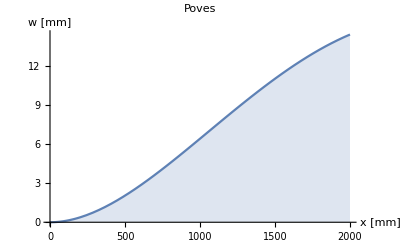

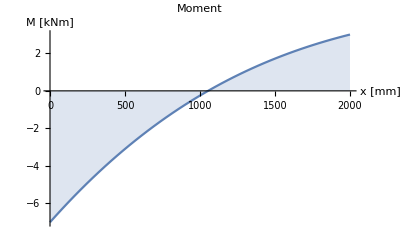

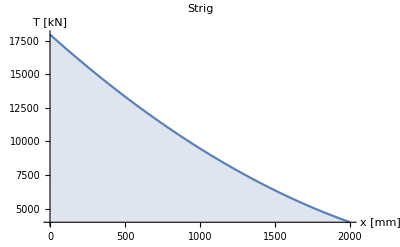

```mathematica
(*izris povesa, notranje strižne sile in notranjega momenta*)
Plot[wn[x],{x,0,L},PlotLabel-> "Poves",AxesLabel->{"x [mm]","w [mm]"}, Filling-> Axis]
Plot[-wn''[x]Ej Iu 10^-6,{x,0,L},PlotLabel-> "Moment",AxesLabel->{"x [mm]","M [kNm]"}, Filling-> Axis]
Plot[-wn'''[x] Ej Iu 10^(.3),{x,0,L},PlotLabel-> "Strig",AxesLabel->{"x [mm]","T [kN]"}, Filling-> Axis]
```

### Analitično 2

```mathematica
(*Reševanje dif. en. za določitev funkcije povesa*)
Clear[w]
DSolve[{
w''''[x]==qx[x]/(Ej Iu),
w[0]==0,w'[0]==0,
-w'''[L] Ej Iu==F0,-w''[L]Ej Iu==M0},w[x],x];
w[x_]=w[x]/.%[[1]]
```

0.0000102339 x^2-4.38596×10^-9 x^3+6.09162×10^-13 x^4-3.65497×10^-17 x^5

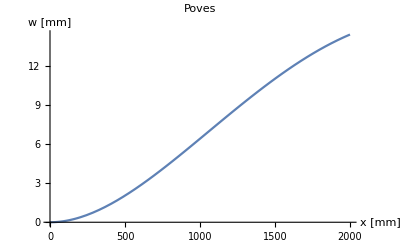

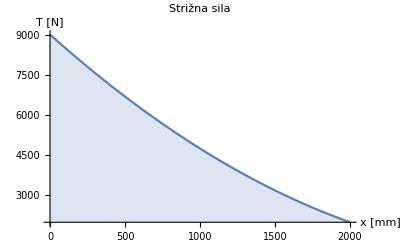

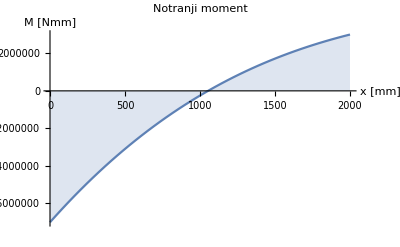

```mathematica
(*izris povesa, notranje strižne sile in notranjega momenta*)
Plot[w[x],{x,0,L},PlotLabel-> "Poves",AxesLabel->{"x [mm]","w [mm]"}]
Plot[-w'''[x]Ej Iu,{x,0,L},PlotLabel-> "Strižna sila",AxesLabel->{"x [mm]","T [N]"},Filling->Axis]
Plot[-w''[x]Ej Iu,{x,0,L},PlotLabel-> "Notranji moment",AxesLabel->{"x [mm]","M [Nmm]"},Filling->Axis]
```

```mathematica
(*Določitev reakcij iz funkcije povesa nosilca*)
Az=-w'''[0]Ej Iu;
Ma=w''[0]Ej Iu;
Print["strižna sila Az=",Az,"N in reakcijski moment ","Ma=",Ma,"Nmm"]
```

strižna sila Az=9000.N in reakcijski moment Ma=7.×10^6Nmm

### MKR

{1.85497,0.408187,-1.05471×10^-15,0.408187,1.43392,2.90035,4.65123,6.54947,8.47579,10.3273,12.0159,13.4674,14.6194,15.4206,15.8288}

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 0 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1)(1.85497
0.408187
-1.05471×10^-15
0.408187
1.43392
2.90035
4.65123
6.54947
8.47579
10.3273
12.0159
13.4674
14.6194
15.4206
15.8288)=(0
0
0.0935673
0.350877
0.0233918
0.0219883
0.0205848
0.0191813
0.0177778
0.0163743
0.0149708
0.0135673
0.0121637
0.0107602
0.00935673)

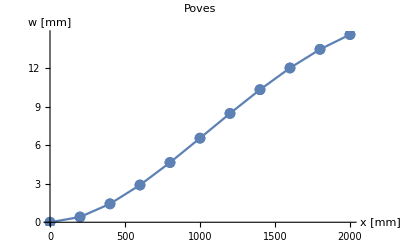

```mathematica
(*diskretizacija*)
del=10;
h=L/del;
n=del+5;
(*definiramo matriko, vektorje*)
M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];
(*RP*)
M[[1,3]]=1;
M[[2,{2,4}]]={-1,1};
M[[3,{-5,-4,-3,-2,-1}]]={1,-2,0,2,-1};
b[[3]]=2 h^3 F0/(Ej Iu);
M[[4,{-4,-3,-2}]]={-1,2,-1};
b[[4]]=h^2 M0/(Ej Iu);
(*DE*)
For[i=1,i≤del+1,i++,
M[[i+4,{i,i+1,i+2,i+3,i+4}]]={1,-4,6,-4,1};
b[[i+4]]=h^4 qx[(i-1)h]/(Ej Iu);
]
wi=LinearSolve[M,b]
Print[MatrixForm[M],MatrixForm[wi],"=",MatrixForm[b]]
(*izris povesa*)
ListLinePlot[Table[{(i-1)h,wi[[i+2]]},{i,1,n-4}],AxesLabel->{"x [mm]","w [mm]"},PlotLabel->"Poves",Mesh->Full]
```

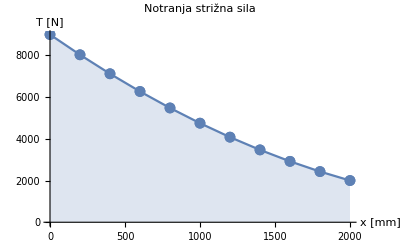

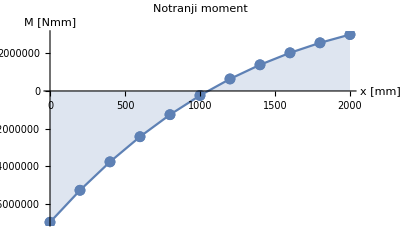

```mathematica
(*Notranja strižna sila in moment*)
Tn=Table[0,{i,1,del+1}];
Mn=Table[0,{i,1,del+1}];
For[i=1,i≤del+1,i++,
Tn[[i]]=-(Ej Iu)/(2 h^3)(-wi[[i]]+2wi[[i+1]]-2wi[[i+3]]+wi[[i+4]]);
Mn[[i]]=-(Ej Iu)/h^2(wi[[i+1]]-2wi[[i+2]]+wi[[i+3]])
]
ListLinePlot[Table[{(i-1)h,Tn[[i]]},{i,1,del+1}],AxesLabel->{"x [mm]","T [N]"},PlotLabel->"Notranja strižna sila", Mesh->Full,Filling->Axis]
ListLinePlot[Table[{(i-1)h,Mn[[i]]},{i,1,del+1}],AxesLabel->{"x [mm]","M [Nmm]"},PlotLabel->"Notranji moment",Mesh->Full,Filling->Axis]
```

## Naloga 2

```mathematica
L=3000.;
M0=1. 10^6;
Ej=200000.;
Iu=171. 10^4;
q0=3.;
qx[x_]=q0 Sin[x/(2L)π];
```

### Analitično

```mathematica
Clear[w]
NDSolve[{
w''''[x]==qx[x]/(Ej Iu),
w[0]==0,w''[0]==M0/(Ej Iu),
w[L]==0,w'[L]==0
},w,{x,0,L}];
(*Izris*)
w[x_]=w[x]/.%[[1]];
pwa=Plot[w[x],{x,0,L},PlotLabel->"Upogib analitično",AxesLabel->{"x [mm]","w [mm]"}];
pTa=Plot[-w'''[x]Ej Iu,{x,0,L-3},PlotLabel->"Strig analitično",AxesLabel->{"x [mm]","T [N]"}];
pMa=Plot[-w''[x]Ej Iu,{x,0,L},PlotLabel->"Moment analitično",AxesLabel->{"x [mm]","M [Nmm]"}];
```

### MKR

```mathematica
(*diskretizacija*)
del=20;
h=L/del;
n=del+5;
(*definiramo matriko in vektor*)
M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];
(*RP*)
M[[1,3]]=1;
M[[2,{2,3,4}]]={1,-2,1};
b[[2]]=(h^2 M0)/(Ej Iu);
M[[3,-3]]=1;
M[[4,{-4,-2}]]={-1,1};
(*DE*)
For[i=1,i≤del+1,i++,
M[[i+4,{i,i+1,i+2,i+3,i+4}]]={1,-4,6,-4,1};
b[[i+4]]=(h^4 qx[(i-1)h])/(Ej Iu);
]
wi=LinearSolve[M,b];
Print[MatrixForm[M],MatrixForm[wi],"=",MatrixForm[b]];
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1)(-0.0204941
-0.0519843
0.
0.117774
0.283652
0.480298
0.69107
0.900362
1.09394
1.25928
1.38585
1.46546
1.49252
1.46433
1.38133
1.24733
1.06974
0.859751
0.63251
0.407273
0.207515
0.0610306
5.42243×10^-18
0.0610306
0.285171)=(0
0.0657895
0
0
0.
0.00034842
0.000694693
0.00103668
0.00137228
0.00169942
0.00201608
0.00232031
0.00261023
0.00288406
0.00314011
0.0033768
0.00359267
0.0037864
0.00395677
0.00410275
0.00422344
0.00431809
0.00438612
0.0044271
0.00444079)

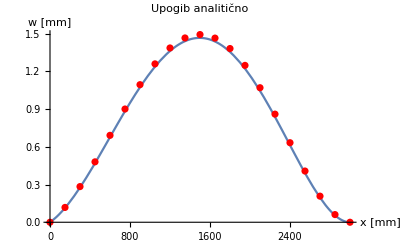

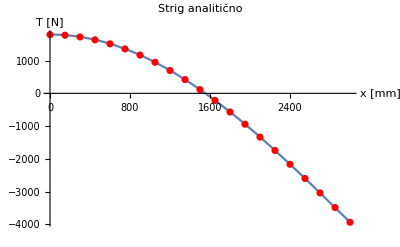

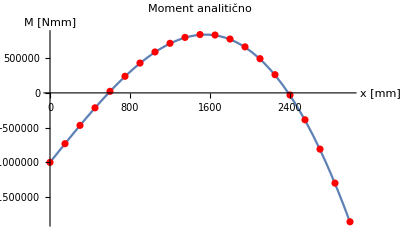

```mathematica
(*izris*)
Ti=Table[0,{i,1,del+1}];
Mi=Table[0,{i,1,del+1}];
For[i=1,i≤del+1,i++,
Ti[[i]]=-(Ej Iu)/(2 h^3)(-wi[[i]]+2wi[[i+1]]-2wi[[i+3]]+wi[[i+4]]);
Mi[[i]]=-(Ej Iu)/h^2(wi[[i+1]]-2wi[[i+2]]+wi[[i+3]])
]
pw=ListPlot[Table[{(i-1)h,wi[[i+2]]},{i,1,n-4}],PlotStyle->Red];
pT=ListPlot[Table[{(i-1)h,Ti[[i]]},{i,1,n-4}],PlotStyle->Red];
pM=ListPlot[Table[{(i-1)h,Mi[[i]]},{i,1,n-4}],PlotStyle->Red];
Show[pwa,pw,PlotRange-> All]
Show[pTa,pT,PlotRange-> All]
Show[pMa,pM,PlotRange-> All]
```

```mathematica
(*reakcije*)
Aza=w'''[0]Ej Iu;
Bza=-w'''[L]Ej Iu;
MBa=-w''[L]Ej Iu;
Print["Analitična rešitev: Az=",Aza," N, Bz=",Bza," N in MB=",MBa," Nmm"]
Az=-Ti[[1]];
Bz=Ti[[-1]];
MB=Mi[[-1]];
Print["MKR rešitev: Az=",Az," N, Bz=",Bz," N in MB=",MB," Nmm"]
```

Analitična rešitev: Az=-1794.67 N, Bz=-3934.9 N in MB=-1.86203×10^6 Nmm

MKR rešitev: Az=-1792.08 N, Bz=-3934.55 N in MB=-1.85533×10^6 Nmm

## Naloga 3

```mathematica
L=3000.;
F0=2. 10^3;
Ej=200000.;
Iu=171. 10^4;
q0=3.;
qx[x_]=q0 Sin[x/(2L)π];
```

### Analitično

```mathematica
Clear[w]
NDSolve[{
w''''[x]==qx[x]/(Ej Iu),
w'''[0]==F0/(Ej Iu),w''[0]==0,
w[L]==0,w'[L]==0
},w[x],x];
w[x_]=w[x]/.%[[1]];
pwa=Plot[w[x],{x,0,L},PlotLabel->"Upogib"];
pTa=Plot[-w'''[x]Ej Iu,{x,0,L},PlotLabel->"Strig",Filling->Axis];
pMa=Plot[-w''[x]Ej Iu,{x,0,L},PlotLabel->"Moment",Filling->Axis];
```

### MKR

```mathematica
(*diskr.*)
del=20;
h=L/del;
n=del+5;
(*matrika, vek.*)
M=Table[0,{i,1,n},{j,1,n}];
b=Table[0,{i,1,n}];
(*RP*)
M[[1,{1,2,4,5}]]={-1,2,-2,1};
b[[1]]=(2 h^3 F0)/(Ej Iu);
M[[2,{2,3,4}]]={1,-2,1};
M[[3,-3]]=1;
M[[4,{-4,-2}]]={-1,1};
(*DE*)
For[i=1,i≤del+1,i++,
M[[i+4,{i,i+1,i+2,i+3,i+4}]]={1,-4,6,-4,1};
b[[i+4]]=(qx[(i-1)h] h^4)/(Ej Iu);
]
wi=LinearSolve[M,b];

Print[MatrixForm[M],MatrixForm[wi],"=",MatrixForm[b]]
```

(-1 | 2 | 0 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 6 | -4 | 1)(98.9062
92.8422
86.7585
80.6748
74.6109
68.5867
62.6232
56.742
50.9665
45.3215
39.8339
34.5329
29.4503
24.621
20.0826
15.8766
12.0476
8.64442
5.71948
3.3295
1.53539
0.402355
1.15433×10^-16
0.402355
1.68789)=(0.0394737
0
0
0
0.
0.00034842
0.000694693
0.00103668
0.00137228
0.00169942
0.00201608
0.00232031
0.00261023
0.00288406
0.00314011
0.0033768
0.00359267
0.0037864
0.00395677
0.00410275
0.00422344
0.00431809
0.00438612
0.0044271
0.00444079)

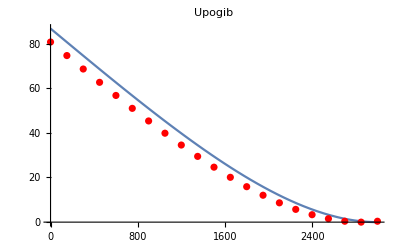

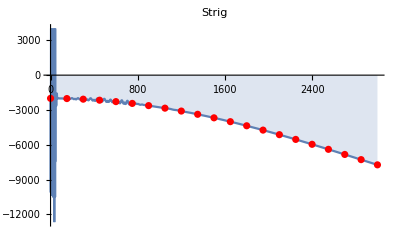

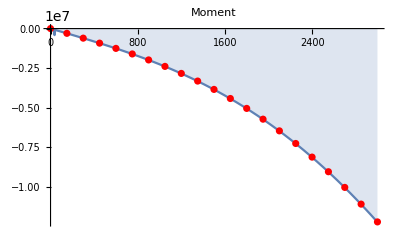

```mathematica
Tn=Table[0,{i,1,del+1}];
Mn=Table[0,{i,1,del+1}];
For[i=1,i≤ del+1,i++,
Tn[[i]]=-(Ej Iu)/(2 h^3)(-wi[[i]]+2wi[[i+1]]-2wi[[i+3]]+wi[[i+4]]);
Mn[[i]]=-(Ej Iu)/h^2(wi[[i+1]]-2wi[[i+2]]+wi[[i+3]]);
]
pw=ListPlot[Table[{(i-1)h,wi[[i+3]]},{i,1,n-4}],PlotStyle->Red];
pT=ListPlot[Table[{(i-1)h,Tn[[i]]},{i,1,n-4}],PlotStyle->Red];
pM=ListPlot[Table[{(i-1)h,Mn[[i]]},{i,1,n-4}],PlotStyle->Red];
Show[pwa,pw,PlotRange-> All]
Show[pTa,pT,PlotRange-> All]
Show[pMa,pM,PlotRange-> All]
```

## Priprave za vajo 2

- obravnava odziva nosilcev v ravnini
- obravnava okvirnih konstrukcij (angl. frame structures)
- določitev pomikov in napetostnega stanja okvirnih konstrukcij (oz. nosilcev) v ravnini

## Naloga 1

Reševanje nosilca in palice.
-Graphics-

```mathematica
Ej = 210000;
Au=1000;
Iu=150 10^4;
F=2000.;
L=2000.;
α=30°;
q0=1;
```

### Analitika

```mathematica
(*Reševanje*)
w1[x_]=c0+c1 x+c2 x^2+c3 x^3+c4 x^4;
u1[x_]=d0+d1 x+d2 x^2;
N1[x_]:=Ej Au u1'[x];
M1[x_]:=-Ej Iu w1''[x];
T1[x_]:=M1'[x];

rez=NSolve[{
u1[0]==0,w1[0]==0, w1'[0]==0,

-N1[L] Sin[α]+T1[L]Cos[α]==0,
N1[L]Cos[α]+T1[L]Sin[α]-F==0,
M1[L]==0,
w1''''[x]==(q0 Sin[α])/(Ej Iu),
Ej Au u1''[x]==-q0 Cos[α]

}]
{w1[x_],u1[x_]}={w1[x],u1[x]}/.Flatten@rez;
```

{{c0→0.,c1→0.,c2→4.7619×10^-6,c3→-1.0582×10^-9,c4→6.61376×10^-14,d0→0.,d1→0.0000164957,d2→-2.06197×10^-9}}

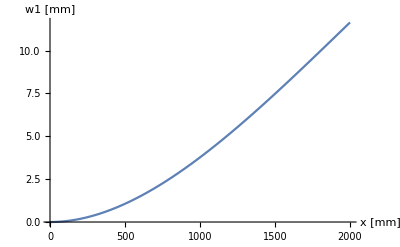

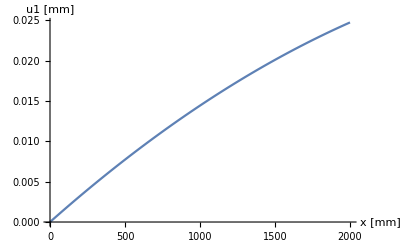

```mathematica
(*Lokalni poves in raztezek*)
Plot[{w1[x]},{x,0,L}, AxesLabel->{"x [mm]","w1 [mm]"}]
Plot[{u1[x]},{x,0,L}, AxesLabel->{"x [mm]","u1 [mm]"}]
```

```mathematica
(*globalni pomiki*)
{ug2,vg2}= {u1[L] Sin[α]-w1[L]Cos[α],-u1[L]Cos[α]-w1[L]Sin[α]}
```

{-10.0683,-5.84153}

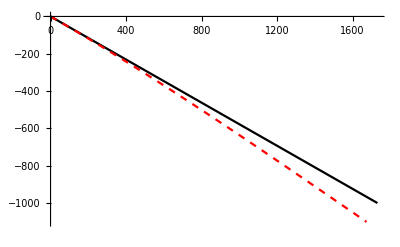

```mathematica
p1=ListLinePlot[{{0,0},{L Cos[α],-L Sin[α]}},PlotStyle->Black];
p2=ParametricPlot[RotationMatrix[-α].{x+10*u1[x],-10*w1[x]},{x,0,L},
PlotStyle->{Dashed,Red}];
Show[p1,p2,PlotRange->All]
```

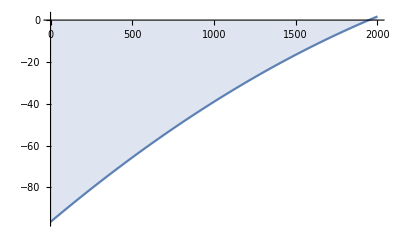

```mathematica
(*Napetosti*)
h=100;
σu[x_,y_]=M1[x]/Iu y;
σn[x_]=N1[x]/Au;
Plot[σu[x,h/2]+σn[x],{x,0,L},Filling->Axis,AxesOrigin->{0,0}]
```

## Naloga 2

Obravnavaj ravninsko konstrukcijo.
-Graphics-

```mathematica
Ej = 210000;
Au=1000;
Iu=150 10^4;
F=2000.;
L=2000.;
α=30°;
```

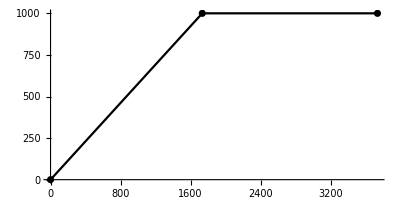

```mathematica
voz={{0,0},L{Cos[α],Sin[α]},L{1+Cos[α],Sin[α]}};
el={{1,2},{2,3}};
p1=Show[ListPlot[voz,PlotStyle-> Black],ListLinePlot[Table[voz[[el[[i]]]],{i,2}],PlotStyle-> Black],AspectRatio->1/2]
```

### Analitika

```mathematica
L1=L2=L;

w1[x_]=c10+c11 x+c12 x^2+c13 x^3;
u1[x_]=d10+d11 x^2;
w2[x_]=c20+c21 x+c22 x^2+c23 x^3;
u2[x_]=d20+d21 x^2;

N1[x_]:=Ej Au u1'[x];
M1[x_]:=-Ej Iu w1''[x];
T1[x_]:=M1'[x];

N2[x_]:=Ej Au u2'[x];
M2[x_]:=-Ej Iu w2''[x];
T2[x_]:=M2'[x];

rez=NSolve[{
u1[0]==0,w1[0]==0,w1'[0]==0,

N2[L2]==F Sin[20°],
T2[L2]==F Cos[20°],
M2[L2]==0,

u1[L1]Cos[α]+w1[L1]Sin[α]==u2[0],
u1[L1]Sin[α]-w1[L1]Cos[α]==-w2[0],
w1'[L1]==w2'[0],
N2[0]-N1[L1]Cos[α]-T1[L1]Sin[α]==0,
-T2[0]+T1[L1]Cos[α]-N1[L1]Sin[α]==0,
M1[L1]==M2[0]
}]
```

{{c10→0.,c11→0.,c12→0.0000111333,c13→-8.61162×10^-10,c20→32.6027,c21→0.0341991,c22→5.9663×10^-6,c23→-9.94384×10^-10,d10→0.,d11→-1.11868×10^-9,d20→18.818,d21→8.14334×10^-10}}

```mathematica
(*globalni pomiki*)
{ug2,vg2}= {u2[0], -w2[0]}/.rez[[1]]
{ug3,vg3}= {u2[L2], -w2[L2]}/.rez[[1]]
```

{18.818,-32.6027}

{18.8213,-116.911}

```mathematica
{u1[x_],w1[x_],u2[x_],w2[x_]}={u1[x],w1[x],u2[x],w2[x]}/.Flatten@rez;
```

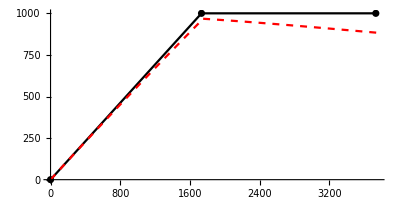

```mathematica
(*izris deformirane lege*)
scal=1;
p2=ParametricPlot[RotationMatrix[α].{x+u1[x],-w1[x]},{x,0,L1},
PlotStyle->{Dashed,Red}];
p3=ParametricPlot[{x+u2[x],-w2[x]}+voz[[2]],{x,0,L2},
PlotStyle->{Dashed,Red}];
Show[p1,p2,p3,PlotRange->All]
```

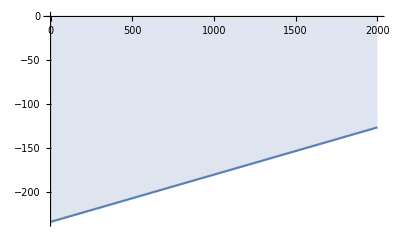

```mathematica
(*Napetosti - element 1*)
h=100;
σu[x_,y_]=M1[x]/Iu y;
σn[x_]=N1[x]/Au;
Plot[σu[x,h/2]+σn[x],{x,0,L1},Filling-> Axis, AxesOrigin->{0,0}]
```

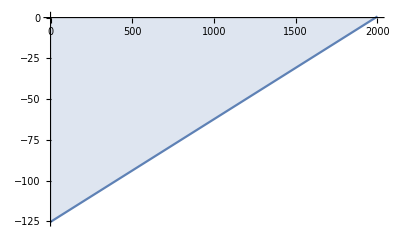

```mathematica
(*Napetosti - element 2*)
h=100;
σu[x_,y_]=M2[x]/Iu y;
σn[x_]=N2[x]/Au;
Plot[σu[x,h/2]+σn[x],{x,0,L2},Filling-> Axis, AxesOrigin->{0,0}]
```

## Priprave za vaje 3, 4, 5, 6

## Priprave na vajo 7

- izpeljava šibke integralske enačbe za 1D in 2D prevod toplote
- izbira (in komentar) aproksimacije za 2D trikotni ter 2D štirikotni KE
- izpeljava ter prikaz (Mathematica) oblikovnih funkcij za omenjene tipe KE
- obravnava 2D izoparametričnega KE (zapis oblikovnih funkcij, preslikava iz naravnih v realne koordinate)

## Izpeljava oblikovnih funkcij v naravnem koordinatnem sistemu za 3-vozliščni končni element

```mathematica
ψ1[x_,y_]=a1+a2 x+a3 y;
```

```mathematica
(* zapis sistema enačb *)
```

```mathematica
Enacbe={ψ1[-1,-1]==1,ψ1[1,-1]==0,ψ1[0,√3/2]==0}
```

{a1-a2-a3==1,a1+a2-a3==0,a1+(√3 a3)/2==0}

```mathematica
Resitev=Solve[Enacbe,{a1,a2,a3}][[1]]
```

{a1→(√3)/(2 (2+√3)),a2→-1/2,a3→-1/(2+√3)}

```mathematica
Ψ1[x_,y_]=FullSimplify[ψ1[x,y]/.Resitev]
```

-3/2+√3-x/2+(-2+√3) y

```mathematica
Plot3D[Ψ1[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

## Izpeljava oblikovnih funkcij v naravnem koordinatnem sistemu za 4-vozliščni končni element

```mathematica
ψ1[x_,y_]=a1+a2 x+a3 y+a4 x y;
```

```mathematica
(* zapis sistema enačb *)
```

```mathematica
Enacbe={ψ1[-1,-1]==1,ψ1[1,-1]==0,ψ1[-1,1]==0,ψ1[1,1]==0}
```

{a1-a2-a3+a4==1,a1+a2-a3-a4==0,a1-a2+a3-a4==0,a1+a2+a3+a4==0}

```mathematica
Resitev=Solve[Enacbe,{a1,a2,a3,a4}][[1]]
```

{a1→1/4,a2→-1/4,a3→-1/4,a4→1/4}

```mathematica
Ψ1[x_,y_]=FullSimplify[ψ1[x,y]/.Resitev]
```

1/4 (-1+x) (-1+y)

```mathematica
Plot3D[Ψ1[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

## Aproksimacija temperaturnega polja znotraj končnega elementa

```mathematica
Ψ1[x_,y_]=1/4 (1-x) (1-y);
Ψ2[x_,y_]=1/4 (1+x) (1-y);
Ψ3[x_,y_]=1/4 (1+x) (1+y);
Ψ4[x_,y_]=1/4 (1-x) (1+y);
```

```mathematica
Taprox[x_,y_]=20 Ψ1[x,y]+34.5 Ψ2[x,y]+33.7 Ψ3[x,y]+20 Ψ4[x,y];
```

```mathematica
Plot3D[Taprox[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Taprox[1/(√3),1/(√3)]
```

30.9382

## Konformnost in zagotavljanje zveznosti primarne spremenljivke

### Generacija pravokotne mreže vozlišč in topologije končnih elementov

```mathematica
Vozlisca={{0,0,0},{1,0,0},{1,1,0},{0,1,0},{2,0,0},{2,1,0}};
Elementi={{1,2,3,4},{2,5,6,3}};
StElem=Length[Elementi];
```

### Izris mreže končnih elementov

```mathematica
ElementPlotNodes=Table[
Graphics3D[Text[Style[i,Large,Bold],Vozlisca[[i]]]]
,{i,1,Length[Vozlisca]}];
ElementPlot=Table[Graphics3D[{Green,Polygon[Vozlisca[[Elementi[[j]]]]]}],{j,1,StElem}];
P1=Show[ElementPlot,ElementPlotNodes]
```

-Graphics3D-

```mathematica
Monomi={1,x,y , x y};
Konstante={a1,a2,a3,a4};
Temp[x_,y_]=Monomi.Konstante
```

a1+a2 x+a3 y+a4 x y

```mathematica
IzracunIzris[el_,T1_,T2_,T3_,T4_,T5_,T6_]:=
Module[{El=el,x1,y1,𝒯1,x2,y2,𝒯2,x3,y3,𝒯3,x4,y4,𝒯4,Res,Temperatura,Ω},
Vozlisca[[;;,3]]={T1,T2,T3,T4,T5,T6};
Clear[Res,𝒯1,𝒯2,𝒯3,𝒯4];
{x1,y1,𝒯1}=Vozlisca[[Elementi[[El]]]][[1]];
{x2,y2,𝒯2}=Vozlisca[[Elementi[[El]]]][[2]];
{x3,y3,𝒯3}=Vozlisca[[Elementi[[El]]]][[3]];
{x4,y4,𝒯4}=Vozlisca[[Elementi[[El]]]][[4]];
Res=Konstante/.Solve[{Temp[x1,y1]==𝒯1,Temp[x2,y2]==𝒯2,Temp[x3,y3]==𝒯3,Temp[x4,y4]==𝒯4},{a1,a2,a3,a4}][[1]];
Temperatura[x_,y_]=Monomi.Res;
Ω=Polygon[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}];
Plot3D[Temperatura[x,y],{x,y}∈Ω,Mesh->None]
]
```

```mathematica
Manipulate[Show[{Show[Table[IzracunIzris[i,T1,T2,T3,T4,T5,T6],{i,1,2}],PlotRange->{0,10},PlotLabel->"Temperatura[x,y]"]},P1],{T1,0,5},{T2,0,5},{T3,0,5},{T4,0,5},{T5,0,5},{T6,0,5}]
```

## Izbira aproksimacijske funkcije v 3D: 8-vozliščni heksaeder

### Koordinate vozlišč v naravnem koordinatnem sistemu in izris tetraedra

Koordinate vozlišč v naravnem koordinatnem sistemu:

```mathematica
Subscript[𝒯, 1]={Subscript[𝓍, 1],Subscript[𝓎, 1],Subscript[𝓏, 1]}={-1,-1,-1};
Subscript[𝒯, 2]={Subscript[𝓍, 2],Subscript[𝓎, 2],Subscript[𝓏, 2]}={+1,-1,-1};
Subscript[𝒯, 3]={Subscript[𝓍, 3],Subscript[𝓎, 3],Subscript[𝓏, 3]}={+1,+1,-1};
Subscript[𝒯, 4]={Subscript[𝓍, 4],Subscript[𝓎, 4],Subscript[𝓏, 4]}={-1,+1,-1};
Subscript[𝒯, 5]={Subscript[𝓍, 5],Subscript[𝓎, 5],Subscript[𝓏, 5]}={-1,-1,+1};
Subscript[𝒯, 6]={Subscript[𝓍, 6],Subscript[𝓎, 6],Subscript[𝓏, 6]}={+1,-1,+1};
Subscript[𝒯, 7]={Subscript[𝓍, 7],Subscript[𝓎, 7],Subscript[𝓏, 7]}={+1,+1,+1};
Subscript[𝒯, 8]={Subscript[𝓍, 8],Subscript[𝓎, 8],Subscript[𝓏, 8]}={-1,+1,+1};
```

```mathematica
Vozlisca=Table[Graphics3D[Text[Style[i,Large,Bold],Subscript[𝒯, i]]],{i,1,8}];
ℛ=Hexahedron[Table[Subscript[𝒯, i],{i,1,8}]];
𝒫f=Show[Graphics3D[{Opacity[0.5],Green,ℛ}],Vozlisca]
```

-Graphics3D-

### Definicija in izris oblikovnih funkcij v naravnem koordinatnem sistemu

Definicija oblikovnih funkcij  Ψ_i(𝓍,𝓎,𝓏), i∈{1,2,...8}:

```mathematica
Subscript[Ψ, i_][𝒳_,𝒴_,𝒵_]=1/8(1+Subscript[𝓍, i]*𝒳)*(1+Subscript[𝓎, i]*𝒴)*(1+Subscript[𝓏, i]*𝒵);
```

```mathematica
Table[Subscript[Ψ, i][𝓍,𝓎,𝓏],{i,1,8}]//MatrixForm (* izpis *)
```

(1/8 (1-𝓍) (1-𝓎) (1-𝓏)
1/8 (1+𝓍) (1-𝓎) (1-𝓏)
1/8 (1+𝓍) (1+𝓎) (1-𝓏)
1/8 (1-𝓍) (1+𝓎) (1-𝓏)
1/8 (1-𝓍) (1-𝓎) (1+𝓏)
1/8 (1+𝓍) (1-𝓎) (1+𝓏)
1/8 (1+𝓍) (1+𝓎) (1+𝓏)
1/8 (1-𝓍) (1+𝓎) (1+𝓏))

Izris oblikovnih funkcij:

```mathematica
k=1;
P1[k_]:=RegionPlot3D[X<100,{X,-1,1},{Y,-1,1},{Z,-1,1},ColorFunction->Function[{X,Y,Z},Hue[Rescale[1-Subscript[Ψ, k][X,Y,Z],{0,1.5}]]],ColorFunctionScaling->False,Mesh->None,PlotStyle->Directive[Opacity[0.8]]];
P2[k_]:=ContourPlot3D[Subscript[Ψ, k][X,Y,Z],{X,-1,1},{Y,-1,1},{Z,-1,1},Contours->5,PlotLegends->"Expressions",ColorFunction->Function[{X,Y,Z},ColorData["Rainbow"][10 Subscript[Ψ, k][X,Y,Z]]],Mesh->False];
Manipulate[Show[P1[k],P2[k]],{k,1,8,1}]
```

### Preslikava iz naravnega v kartezijev (realni) koordinatni sistem

Koordinate vozlišč v kartezijevem koordinatnem sistemu:

```mathematica
Subscript[T, 1]={Subscript[x, 1],Subscript[y, 1],Subscript[z, 1]}={0,0,0};
Subscript[T, 2]={Subscript[x, 2],Subscript[y, 2],Subscript[z, 2]}={1,-1/2,0};
Subscript[T, 3]={Subscript[x, 3],Subscript[y, 3],Subscript[z, 3]}={2,1,0};
Subscript[T, 4]={Subscript[x, 4],Subscript[y, 4],Subscript[z, 4]}={1,1,0};
Subscript[T, 5]={Subscript[x, 5],Subscript[y, 5],Subscript[z, 5]}={0,0,1};
Subscript[T, 6]={Subscript[x, 6],Subscript[y, 6],Subscript[z, 6]}={1,0,1};
Subscript[T, 7]={Subscript[x, 7],Subscript[y, 7],Subscript[z, 7]}={2,1,1};
Subscript[T, 8]={Subscript[x, 8],Subscript[y, 8],Subscript[z, 8]}={3/2,3/2,3/2};
```

Izris dejanske geometrije

```mathematica
Vozlisca=Table[Graphics3D[Text[Style[i,Large,Bold],Subscript[T, i]]],{i,1,8}];
ℛ=Hexahedron[Table[Subscript[T, i],{i,1,8}]];
𝒫1=Show[Graphics3D[{Opacity[0.5],Blue,ℛ}],Vozlisca]
```

-Graphics3D-

Preslikava 𝓍, 𝓎, 𝓏 koordinat v x,y,z :

```mathematica
x[𝒳_,𝒴_,𝒵_]=Sum[Subscript[x, i] Subscript[Ψ, i][𝒳,𝒴,𝒵],{i,1,8}]
y[𝒳_,𝒴_,𝒵_]=Sum[Subscript[y, i] Subscript[Ψ, i][𝒳,𝒴,𝒵],{i,1,8}]
z[𝒳_,𝒴_,𝒵_]=Sum[Subscript[z, i] Subscript[Ψ, i][𝒳,𝒴,𝒵],{i,1,8}]
```

1/8 (1+𝒳) (1-𝒴) (1-𝒵)+1/8 (1-𝒳) (1+𝒴) (1-𝒵)+1/4 (1+𝒳) (1+𝒴) (1-𝒵)+1/8 (1+𝒳) (1-𝒴) (1+𝒵)+3/16 (1-𝒳) (1+𝒴) (1+𝒵)+1/4 (1+𝒳) (1+𝒴) (1+𝒵)

-1/16 (1+𝒳) (1-𝒴) (1-𝒵)+1/8 (1-𝒳) (1+𝒴) (1-𝒵)+1/8 (1+𝒳) (1+𝒴) (1-𝒵)+3/16 (1-𝒳) (1+𝒴) (1+𝒵)+1/8 (1+𝒳) (1+𝒴) (1+𝒵)

1/8 (1-𝒳) (1-𝒴) (1+𝒵)+1/8 (1+𝒳) (1-𝒴) (1+𝒵)+3/16 (1-𝒳) (1+𝒴) (1+𝒵)+1/8 (1+𝒳) (1+𝒴) (1+𝒵)

### Grafična uprizoritev preslikave izbrane točke

```mathematica
Manipulate[Row[{Show[𝒫f,Graphics3D[{PointSize[Large],Red,Point[{𝓍,𝓎,𝓏}]}]],Show[𝒫1,Graphics3D[{PointSize[Large],Red,Point[{x[𝓍,𝓎,𝓏],y[𝓍,𝓎,𝓏],z[𝓍,𝓎,𝓏]}]}],Graphics3D[Text[Style[{x[𝓍,𝓎,𝓏],y[𝓍,𝓎,𝓏],z[𝓍,𝓎,𝓏]},Medium,Red],{x[𝓍,𝓎,𝓏]+0.1,y[𝓍,𝓎,𝓏]+0.1,z[𝓍,𝓎,𝓏]+0.1}]]]}],{𝓍,-1,1},{𝓎,-1,1},{𝓏,-1,1}]
```

OBRATNA POT: Kam se točka iz realne geometrije (modri heksaeder) slika v pomožno geometrijo (zeleni heksaeder)?

```mathematica
(* koordinate točke na realni geometriji *)
X=1;
Y=0.4;
Z=0.5;
```

```mathematica
(* koordinate točke na pomožni geometriji *)
Solve[{X==x[𝒳,𝒴,𝒵],Y==y[𝒳,𝒴,𝒵],Z==z[𝒳,𝒴,𝒵],-1≤𝒳≤1,-1≤𝒴≤1,-1≤𝒵≤1},{𝒳,𝒴,𝒵}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{𝒳→0.0389473,𝒴→-0.133252,𝒵→-0.0943045}}

## Naloge

-Graphics-

### 2D trikotni KE

```mathematica
(*Podatki*)
{T1,T2,T3}={20,30,33}(*oC*);
{{xi,yi},{xj,yj},{xk,yk}}={{2,5},{5,3},{4,8}};
(*Oblikovne funkcije*)
ψi[x_,y_]=a0+a1 x+a2 y;
ψj[x_,y_]=b0+b1 x+b2 y;
ψk[x_,y_]=c0+c1 x+c2 y;
rezi=Solve[{ψi[xi,yi]==1,ψi[xj,yj]==0,ψi[xk,yk]==0}];
rezj=Solve[{ψj[xi,yi]==0,ψj[xj,yj]==1,ψj[xk,yk]==0}];
rezk=Solve[{ψk[xi,yi]==0,ψk[xj,yj]==0,ψk[xk,yk]==1}];
ψi[x_,y_]=ψi[x,y]/.rezi[[1]];
ψj[x_,y_]=ψj[x,y]/.rezj[[1]];
ψk[x_,y_]=ψk[x,y]/.rezk[[1]];
```

```mathematica
Plot3D[{ψi[x,y],ψj[x,y],ψk[x,y]},{x,y}∈Polygon[{{xi,yi},{xj,yj},{xk,yk}}]]
```

-Graphics3D-

```mathematica
(*Aproksimacija temp.*)
Tapr[x_,y_]=T1 ψi[x,y]+T2 ψj[x,y]+T3 ψk[x,y];
Plot3D[Tapr[x,y],{x,y}∈Polygon[{{xi,yi},{xj,yj},{xk,yk}}]]
```

-Graphics3D-

### 2D štirikotni (8-voz.) KE (v naravnem KS)

```mathematica
ψ1[x_,y_]=a1 +a2 x+a3 y+a4 x^2+a5 x y + a6 y^2+a7 x^2 y+a8 x y^2;
rez=Solve[{
ψ1[-1,-1]==1,
ψ1[1,-1]==0,
ψ1[1,1]==0,
ψ1[-1,1]==0,
ψ1[0,-1]==0,
ψ1[1,0]==0,
ψ1[0,1]==0,
ψ1[-1,0]==0
}]
ψ1[x_,y_]=ψ1[x,y]/.rez[[1]];
Plot3D[ψ1[x,y],{x,y}∈Polygon[{{-1,-1},{1,-1},{1,1},{-1,1}}],PlotRange->All]
```

{{a1→-1/4,a2→0,a3→0,a4→1/4,a5→1/4,a6→1/4,a7→-1/4,a8→-1/4}}

-Graphics3D-

### Naloga - primer trikotni KE

-Graphics-

```mathematica
(*podatki*)
koord={{0,0},{5,3},{0,8}};
k=10;
q1=5;
q2=10;
T0=100;
L1=EuclideanDistance[{0,0},{5,3}];
L2=EuclideanDistance[{5,3},{0,8}];

(*Oblikovne funkcije*)
{{xi,yi},{xj,yj},{xk,yk}}=koord;
obmocje=Polygon[koord];
A=Area[obmocje];
ψi[x_,y_]=1/(2 A)(xj yk-xk yj + (yj-yk) x + (xk-xj) y);
ψj[x_,y_]=1/(2 A)(xk yi-xi yk + (yk-yi) x + (xi-xk) y);
ψk[x_,y_]=1/(2 A)(xi yj-xj yi + (yi-yj) x + (xj-xi) y);
(*matrika odvodov*)
B=({{D[ψi[x,y],x], D[ψj[x,y],x], D[ψk[x,y],x]}, {D[ψi[x,y],y], D[ψj[x,y],y], D[ψk[x,y],y]}});
(*Ke*)
Ke=k Integrate[ Bᵀ.B,{x,y}∈obmocje];
T1=T3=T0;
(*Rezultat*)
Solve[Ke.({{T1}, {T2}, {T3}})==-(({{q1 L1/2}, {q1 L1/2}, {0}})+({{0}, {q2 L2/2}, {q2 L2/2}})+({{qR1}, {0}, {qR3}}))]//N
```

{{qR1→-45.7853,qR3→-54.0801,T2→93.7584}}

### Naloga - primer štirikotni KE

-Graphics-

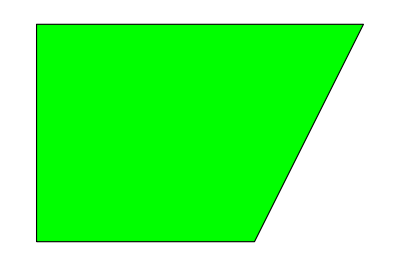

```mathematica
(*Podatki*)
k=10.;
T1=30.;
T4=30.;
q1=5.;
q2=10.;
L1=EuclideanDistance[voz[[1]],voz[[2]]];
L2=EuclideanDistance[voz[[2]],voz[[3]]];
L3=EuclideanDistance[voz[[3]],voz[[4]]];
L4=EuclideanDistance[voz[[1]],voz[[4]]];
(*Definicija KE*)
voz={{Xi,Yi},{Xj,Yj},{Xk,Yk},{Xl,Yl}}={{0.,0.},{10.,0.},{15.,10.},{0.,10.}};
ele={{1,2,3,4}};
Ω=Polygon[voz];
Graphics[{Green,EdgeForm[Black],Ω}]
```

```mathematica
(*naravni koordinatni sistem*)
vozN={{xi,yi},{xj,yj},{xk,yk},{xl,yl}}={{-1,-1},{1,-1},{1,1},{-1,1}};
ΩN=Polygon[vozN];
(*Oblikovne funkcije - naravni koordinatni sistem*)
ψi[x_,y_]=(xj (xk (yj-yk) (y-yl)-xl (y-yk) (yj-yl))+x (xl (yj-yk) (y-yl)-xk (y-yk) (yj-yl)+xj (y-yj) (yk-yl))+xk xl (y-yj) (yk-yl))/(xj (xk (yj-yk) (yi-yl)-xl (yi-yk) (yj-yl))+xi (xl (yj-yk) (yi-yl)-xk (yi-yk) (yj-yl)+xj (yi-yj) (yk-yl))+xk xl (yi-yj) (yk-yl));
ψj[x_,y_]=(xi (-xk (yi-yk) (y-yl)+xl (y-yk) (yi-yl))+x (-xl (yi-yk) (y-yl)+xk (y-yk) (yi-yl)-xi (y-yi) (yk-yl))-xk xl (y-yi) (yk-yl))/(xj (xk (yj-yk) (yi-yl)-xl (yi-yk) (yj-yl))+xi (xl (yj-yk) (yi-yl)-xk (yi-yk) (yj-yl)+xj (yi-yj) (yk-yl))+xk xl (yi-yj) (yk-yl));
ψk[x_,y_]=(xi (xj (yi-yj) (y-yl)-xl (y-yj) (yi-yl))+x (xl (yi-yj) (y-yl)-xj (y-yj) (yi-yl)+xi (y-yi) (yj-yl))+xj xl (y-yi) (yj-yl))/(xj (xk (yj-yk) (yi-yl)-xl (yi-yk) (yj-yl))+xi (xl (yj-yk) (yi-yl)-xk (yi-yk) (yj-yl)+xj (yi-yj) (yk-yl))+xk xl (yi-yj) (yk-yl));
ψl[x_,y_]=(xi (-xj (yi-yj) (y-yk)+xk (y-yj) (yi-yk))+x (-xk (yi-yj) (y-yk)+xj (y-yj) (yi-yk)-xi (y-yi) (yj-yk))-xj xk (y-yi) (yj-yk))/(xj (xk (yj-yk) (yi-yl)-xl (yi-yk) (yj-yl))+xi (xl (yj-yk) (yi-yl)-xk (yi-yk) (yj-yl)+xj (yi-yj) (yk-yl))+xk xl (yi-yj) (yk-yl));
(*Matrika okdvodov*)
B[x_,y_]=({{D[ψi[x,y],x], D[ψj[x,y],x], D[ψk[x,y],x], D[ψl[x,y],x]}, {D[ψi[x,y],y], D[ψj[x,y],y], D[ψk[x,y],y], D[ψl[x,y],y]}});
(*preslikava koordinat*)
X[x_,y_]={ψi[x,y],ψj[x,y],ψk[x,y],ψl[x,y]}.{Xi,Xj,Xk,Xl};
Y[x_,y_]={ψi[x,y],ψj[x,y],ψk[x,y],ψl[x,y]}.{Yi,Yj,Yk,Yl};
(*Preslikava z Jakobijevo matriko*)
J[x_,y_]=({{D[X[x,y],x], D[Y[x,y],x]}, {D[X[x,y],y], D[Y[x,y],y]}});
detJ[x_,y_]=Det[J[x,y]];
InvJ[x_,y_]=Inverse[J[x,y]];
(*togostna matrika elementa*)
Ke=k Integrate[(InvJ[x,y].B[x,y])ᵀ.(InvJ[x,y].B[x,y]) detJ[x,y],{x,y}∈ΩN];
(*reševanje*)
rez=Solve[Ke.({{T1}, {T2}, {T3}, {T4}})==-({{q1 L1/2+qR1}, {q1 L1/2+q2 L2/2}, {q2 L2/2}, {qR4}})]
```

{{qR1→-89.9797,qR4→-71.8237,T2→15.5459,T3→11.5033}}

```mathematica
(*Temperature in toplotni tok*)
Trez=Flatten@({{T1}, {T2}, {T3}, {T4}})/.rez[[1]]
```

{30.,15.5459,11.5033,30.}

```mathematica
q[x_,y_]=-k(InvJ[x,y].B[x,y]).Trez;
q[0,0]
```

{13.1803,-1.27376}

## Priprave na vajo 8

- Abaqus: Izdelava numerične analize prevoda toplote (2D in 3D)
- izpeljava enačbe tro-vozliščnega KE za analizo 2D časovno ustaljenega prevoda toplota in
- izdelava analize (Mathematica) z uporabo večih KE (t.j. zlaganje KE)

## Izpeljava enačbe tro-vozliščnega KE za 2D časovno-ustaljen prevod toplote

### Izpeljava oblikovnih funkcij ( splošno v odvisnosti od koordinat {{x_1,y_1},{x_2,y_2},{x_3,y_3}} )

Oblikovne funkcije:

```mathematica
-Graphics-;
```

```mathematica
ψ[x_,y_]=a1+a2 x+a3 y;
```

```mathematica
{A1,A2,A3}={a1,a2,a3}/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
{B1,B2,B3}={a1,a2,a3}/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
{C1,C2,C3}={a1,a2,a3}/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
```

```mathematica
ψ1[x_,y_]=A1+A2 x+A3 y
ψ2[x_,y_]=B1+B2 x+B3 y
ψ3[x_,y_]=C1+C2 x+C3 y
```

-((-xj+xk) y)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(-xk yj+xj yk)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(x (-yj+yk))/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk)

-(x (-yi+yk))/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-((-xi+xk) y)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk)-(-xk yi+xi yk)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk)

-(x (yi-yj))/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(-xj yi+xi yj)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-((xi-xj) y)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk)

### Snovanje matrike toplotne prevodnosti v splošnem

Matrika toplotne prevodnosti:

```mathematica
K[k_,{{xi_,yi_},{xj_,yj_},{xk_,yk_}}]:=
Module[{Ωel,Ktoplota,x,y},
Ωel=Polygon[{{xi,yi},{xj,yj},{xk,yk}}];
Subscript[ψ, 1][x_,y_]=-((-xj+xk) y)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(-xk yj+xj yk)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(x (-yj+yk))/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk);
Subscript[ψ, 2][x_,y_]=-(x (-yi+yk))/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-((-xi+xk) y)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk)-(-xk yi+xi yk)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk);
Subscript[ψ, 3][x_,y_]=-(x (yi-yj))/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(-xj yi+xi yj)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-((xi-xj) y)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk);
Ktoplota=k Table[Integrate[D[Subscript[ψ, i][x,y],x]*D[Subscript[ψ, j][x,y],x]+D[Subscript[ψ, i][x,y],y]*D[Subscript[ψ, j][x,y],y],{x,y}∈Ωel],{i,1,3},{j,1,3}]
]
```

Testni izračun:

```mathematica
K[54,{{0,0},{1,0},{1/2,1}}];
MatrixForm[%]
```

(135/4 | -81/4 | -27/2
-81/4 | 135/4 | -27/2
-27/2 | -27/2 | 27)

## Naloga 1

Z uporabo štirih trovozliščnih KE določi temperaturno polje v steni.
-Graphics-

```mathematica
(*Podatki*)
s=100(*mm*);
h=100(*mm*);
T01=20(*oC*);
T02=50(*oC*);
k0=54(*W/m2K*);
```

### Analitična rešitev

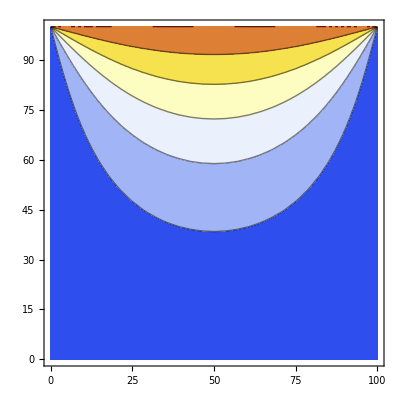

```mathematica
Tanaliticna[x_,y_]=T01+(T02-T01)*2/π *Sum[((-1)^(i+1)+1)/i Sin[(i π x)/s] *Sinh[(i π y)/s]/Sinh[(i π h)/s],{i,1,1000}];
ContourPlot[Tanaliticna[x,y],{x,0,s},{y,0,h},ColorFunction->"Temperature"]
```

### Aproksimativna rešitev (MKE)

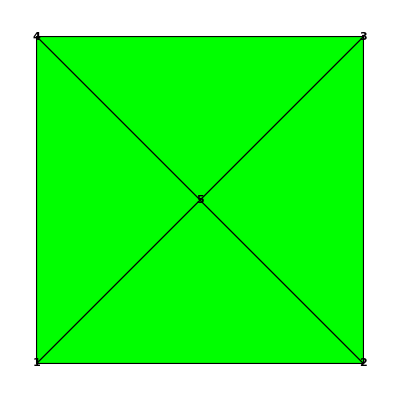

```mathematica
voz={{0,0},{100,0},{100,100},{0,100},{50,50}};
ele={{1,2,5},{2,3,5},{3,4,5},{4,1,5}};

stv=Length[voz];
ste =Length[ele];

(*izris mreže*)
ElementPlotNodes=Table[Graphics[Text[Style[i,Large,Bold],voz[[i]]]],{i,1,stv}];
ElementPlot=Table[Graphics[{Green,EdgeForm[Black],Polygon[voz[[ele[[j]]]]]}],{j,1,ste}];p1=Show[ElementPlot,ElementPlotNodes]
```

#### Snovanje in izračun prevodnostnih matrik za vsak element posebej

```mathematica
(*modul za izračun poljubne matrike*)
K[k_,{{xi_,yi_},{xj_,yj_},{xk_,yk_}}]:=
Module[{Ωel,Ktoplota,x,y},
Ωel=Polygon[{{xi,yi},{xj,yj},{xk,yk}}];
Subscript[ψ, 1][x_,y_]=-((-xj+xk) y)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(-xk yj+xj yk)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(x (-yj+yk))/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk);
Subscript[ψ, 2][x_,y_]=-(x (-yi+yk))/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-((-xi+xk) y)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk)-(-xk yi+xi yk)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk);
Subscript[ψ, 3][x_,y_]=-(x (yi-yj))/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-(-xj yi+xi yj)/(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)-((xi-xj) y)/(-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk);
Ktoplota=k Table[Integrate[D[Subscript[ψ, i][x,y],x]*D[Subscript[ψ, j][x,y],x]+D[Subscript[ψ, i][x,y],y]*D[Subscript[ψ, j][x,y],y],{x,y}∈Ωel],{i,1,3},{j,1,3}]
];
```

```mathematica
(*izračun prevodnostnih matrik za vse elemente*)
KvsiElementi=Table[f[i],{i,1,ste}];
For[i=1,i≤ ste,i++,
KoordVozElem=voz[[ele[[i]]]];
KvsiElementi[[i]]=K[k0, KoordVozElem];
Print["el ",i,": ",ele[[i]],"  Kel=",MatrixForm[KvsiElementi[[i]]]];
]
```

el 1: {1,2,5}  Kel=(27 | 0 | -27
0 | 27 | -27
-27 | -27 | 54)

el 2: {2,3,5}  Kel=(27 | 0 | -27
0 | 27 | -27
-27 | -27 | 54)

el 3: {3,4,5}  Kel=(27 | 0 | -27
0 | 27 | -27
-27 | -27 | 54)

el 4: {4,1,5}  Kel=(27 | 0 | -27
0 | 27 | -27
-27 | -27 | 54)

#### Zlaganje lokalnih prevodnostnih matrik v globalno matriko

```mathematica
Kglob=Table[0,{i,1,stv},{j,1,stv}];

For[i=1,i≤ ste,i++,
poz=ele[[i]];
Klok=KvsiElementi[[i]];
Kglob[[poz,poz]]=Kglob[[poz,poz]]+Klok;
(*Print[i,".  pozicija: ",poz,"  Kglob=",MatrixForm[Kglob]];*)
]
(*Končna globalna matrika*)
MatrixForm[Kglob]
```

(54 | 0 | 0 | 0 | -54
0 | 54 | 0 | 0 | -54
0 | 0 | 54 | 0 | -54
0 | 0 | 0 | 54 | -54
-54 | -54 | -54 | -54 | 216)

#### Reševanje sistema enačb

```mathematica
Ti=({{T01}, {T01}, {T02}, {T02}, {T5}});
qi=({{R1}, {R2}, {R3}, {R4}, {0}});
Print[MatrixForm[Kglob],MatrixForm[Ti],"=",MatrixForm[qi]]
Solve[Kglob.Ti==qi]
```

(54 | 0 | 0 | 0 | -54
0 | 54 | 0 | 0 | -54
0 | 0 | 54 | 0 | -54
0 | 0 | 0 | 54 | -54
-54 | -54 | -54 | -54 | 216)(20
20
50
50
T5)=(R1
R2
R3
R4
0)

{{R1→-810,R2→-810,R3→810,R4→810,T5→35}}

## Priprave za vaje 9

## Priprave za vajo 10

- obravnava ravninskega napetostnega stanja - STENE
- robni problem STENE: zapis vodilnih enačb problema in robnih pogojev
- obravnava in reševanje problema sten po MKE
- izračun in analiza polja pomikov
- izračun in analiza polja komponentnih napetosti v steni

## Stene MKE - enačbe

### Togostna matrika, matrika oblikovnih funkcij in matrika odvodov oblikovnih funkcij

```mathematica
(* matrika oblikovnih funkcij *)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
```

```mathematica
(* matrika odvodov oblikovnih funkcij *)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
```

```mathematica
(* matrika elastičnih konstant *)
Dm=Em/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
```

```mathematica
(* togostna matrika *)
```

```mathematica
Kstene=t*Beᵀ.Dm.Be*Ael;
```

### Oblikovne funkcije -- trikotni končni element

```mathematica
(* {{xi,yi},{xj,yj},{xk,yk}} - koordinate vozlišč elementa *)
```

```mathematica
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
```

## Naloga 1

Pristop reševanja problema, izpeljava togostne matrike problema z enim končnim elementom, zapis robnih pogojev in reševanje sistema enačb. Potek programiranja v Mathematici
-Graphics-

```mathematica
(*Podatki*)
a=100.(*mm*);
Ej=210000.(*MPa*);
ν=0.3;
t=1.;(*mm*)
F0=1000(*N*);
(* matrika elastičnih konstant *)
Dm=Ej/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
```

### Reševanje

```mathematica
(*vozlišča in površina*)
voz={{xi,yi},{xj,yj},{xk,yk}}={{0,0},{a/2,0},{a/2,√3 a/2}};
Ω=Polygon[voz];
Ael=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(* matrika odvodov oblikovnih funkcij *)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(* togostna matrika *)
Kstene=t*Beᵀ.Dm.Be*Ael;
(*Robni pogoji*)
U={0,0,0,V2,0,V3};
F={F1x, F1y, F2x, 0, F3x, -F0/2};
(*reševanje*)
r=Solve[Kstene.U==F]
Ur=U/.r[[1]];
```

{{F1x→259.808,F1y→500.,F2x→28.8675,F3x→-288.675,V2→-0.00714815,V3→-0.0146537}}

```mathematica
(*napetosti*)
σ=Dm.Be.Ur
```

{-6.,-20.,-11.547}

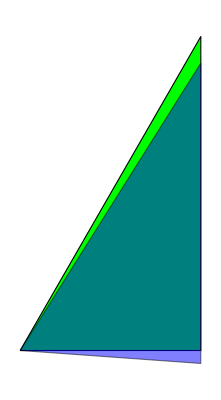

```mathematica
(*izris*)
u=Partition[Ur,2];
skal=500;
p1=Graphics[{Green, EdgeForm[Black], Polygon[voz]}];
p2=Graphics[{Blue,Opacity[0.5], EdgeForm[Black], Polygon[voz+skal*u]}];
Show[p1,p2]
```

## Naloga 2

Pristop reševanja problema, izpeljava togostne matrike problema z enim končnim elementom, zapis robnih pogojev in reševanje sistema enačb.
Potek programiranja v Mathematici
-Graphics-

```mathematica
(*Podatki*)
a=100.(*mm*);
Ej=210000.(*MPa*);
ν=0.3;
t=1.;(*mm*)
F0=1000(*N*);
(* matrika elastičnih konstant *)
Dm=Ej/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
```

### Reševanje

```mathematica
(*vozlišča in površina*)
voz={{0,0},{a/2,0},{a/4,√3 a/4}, {a/2, √3 a/2}};
el={{1,2,3},{2,4,3}};
```

#### element 1

```mathematica
(*koordinate*)
koord={{xi,yi},{xj,yj},{xk,yk}}={voz[[1]],voz[[2]],voz[[3]]};
Ω=Polygon[koord];
Ael1=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(* matrika odvodov oblikovnih funkcij *)
B1=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(* togostna matrika *)
K1=t*B1ᵀ.Dm.B1*Ael1;
```

#### element 2

```mathematica
(*koordinate*)
koord={{xi,yi},{xj,yj},{xk,yk}}={voz[[2]],voz[[4]],voz[[3]]};
Ω=Polygon[koord];
Ael2=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(* matrika odvodov oblikovnih funkcij *)
B2=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(* togostna matrika *)
K2=t*B2ᵀ.Dm.B2*Ael2;
```

#### Sistemska togostna matrika

```mathematica
Kglob=ConstantArray[0,{8,8}];
Kglob[[{1,2,3,4,5,6},{1,2,3,4,5,6}]]+=K1;
Kglob[[{3,4,7,8,5,6},{3,4,7,8,5,6}]]+=K2;
```

#### Robni pogoji in reševanje

```mathematica
(*Robni pogoji*)
U={0,0,0,V2,U3,V3, 0, V4};
F={Ax, Ay, Bx, 0, 0,0, Cx, -F0/2};
(*reševanje*)
r=Solve[Kglob.U==F]
Ur=U/.r[[1]];
```

{{Ax→274.237,Ay→500.,Bx→14.4383,Cx→-288.675,U3→0.0000793403,V2→-0.00723753,V3→-0.00737271,V4→-0.0146583}}

```mathematica
(*Napetosti*)
```

```mathematica
σ1=Dm.B1.Ur[[{1,2,3,4,5,6}]]
σ2=Dm.B2.Ur[[{3,4,7,8,5,6}]]
```

{-6.00188,-20.0063,-11.5434}

{-6.66458,-19.9937,-11.5506}

#### Izris

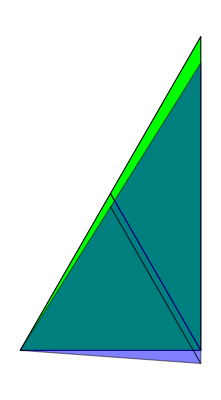

```mathematica
(*izris*)
u=Partition[Ur,2];
skal=500;
p1=Table[Graphics[{Green, EdgeForm[Black], Polygon[voz[[el[[i]]]]]}], {i,1,2}];
p2=Table[Graphics[{Blue,Opacity[0.5], EdgeForm[Black], Polygon[voz[[el[[i]]]]+skal*u[[el[[i]]]]]}], {i,1,2}];
Show[p1,p2]
```

### Reševanje z poljubnim številom KE

```mathematica
(*vozlišča in površina*)
voz={{0,0},{a/2,0},{a/4,√3 a/4}, {a/2, √3 a/2}};
el={{1,2,3},{2,4,3}};

stv = Length[voz];
ste=Length[el];
```

#### Zanka za elemente in globalna togostna matrika

```mathematica
Kglob=ConstantArray[0,{2 stv,2stv}];
Bvsi=Table[0,{k,1,ste}];

For[k=1,k≤ste,k++,
v=el[[k]];
m={2v[[1]]-1,2 v[[1]],2 v[[2]]-1,2 v[[2]],2 v[[3]]-1,2v[[3]]};
(*koordinate*)
koordinate={{xi,yi},{xj,yj},{xk,yk}}=voz[[v]];
Ω=Polygon[koordinate];
Ael=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(* matrika odvodov oblikovnih funkcij *)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
Bvsi[[k]]=Be;
(* togostna matrika *)
Ke=t*Beᵀ.Dm.Be*Ael;
Kglob[[m,m]]+=Ke;

Print["element: ", k, " vozlišča: ", v, " mesta v tm: ",m];
]
Kglob//MatrixForm
```

element: 1 vozlišča: {1,2,3} mesta v tm: {1,2,3,4,5,6}

element: 2 vozlišča: {2,4,3} mesta v tm: {3,4,7,8,5,6}

(111584. | 37500. | -88268. | -2884.62 | -23316.1 | -34615.4 | 0 | 0
37500. | 68282.8 | 2884.62 | -1665.43 | -40384.6 | -66617.3 | 0 | 0
-88268. | 2884.62 | 223168. | -75000. | -223168. | 75000. | 88268. | -2884.62
-2884.62 | -1665.43 | -75000. | 136566. | 75000. | -136566. | 2884.62 | 1665.43
-23316.1 | -40384.6 | -223168. | 75000. | 446336. | 0. | -199852. | -34615.4
-34615.4 | -66617.3 | 75000. | -136566. | 0. | 273131. | -40384.6 | -69948.2
0 | 0 | 88268. | 2884.62 | -199852. | -40384.6 | 111584. | 37500.
0 | 0 | -2884.62 | 1665.43 | -34615.4 | -69948.2 | 37500. | 68282.8)

#### Robni pogoji in reševanje

```mathematica
(*Robni pogoji*)
U={0,0,0,V2,U3,V3, 0, V4};
F={Ax, Ay, Bx, 0, 0,0, Cx, -F0/2};
(*reševanje*)
r=Solve[Kglob.U==F]
Ur=U/.r[[1]];
```

{{Ax→274.237,Ay→500.,Bx→14.4383,Cx→-288.675,U3→0.0000793403,V2→-0.00723753,V3→-0.00737271,V4→-0.0146583}}

```mathematica
(*Napetosti*)
```

```mathematica
For[k=1,k≤ste,k++,
v=el[[k]];
m={2v[[1]]-1,2 v[[1]],2 v[[2]]-1,2 v[[2]],2 v[[3]]-1,2v[[3]]};
Be=Bvsi[[k]];
σel=Dm.Be.Ur[[m]];
Print["element: ", k, " vozlišča: ", v, " napetosti: ",σel];
]
```

element: 1 vozlišča: {1,2,3} napetosti: {-6.00188,-20.0063,-11.5434}

element: 2 vozlišča: {2,4,3} napetosti: {-6.66458,-19.9937,-11.5506}

#### Izris

```mathematica
(*izris*)
u=Partition[Ur,2];
skal=500;
p1=Table[Graphics[{Green, EdgeForm[Black], Polygon[voz[[el[[i]]]]]}], {i,1,2}];
p2=Table[Graphics[{Blue,Opacity[0.5], EdgeForm[Black], Polygon[voz[[el[[i]]]]+skal*u[[el[[i]]]]]}], {i,1,2}];
Show[p1,p2]
```

-Graphics-

## Naloga 3

Za prikazani primer tankega bimetalnega elementa izračunajte: 
- vozliščne pomike in 
- komponente napetostnega tenzorja
-Graphics-

```mathematica
(*Podatki*)
F=1000.(*N*);
ΔT=100.(*oC*);
H=2.(*mm*);
L=20.(*mm*);
t=10.(*mm*);
Ej=210000.(*MPa*);
Eb=120000.(*MPa*);
ν=0.3;
αj=12 10^-6;
αb=18 10^-6;

(* vektor materialnih konstant *)
Evsi={Eb,Eb,Ej,Ej};
αvsi={αb,αb,αj,αj};
```

### Definiramo vozlišča in končne elemente

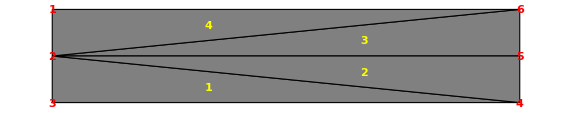

```mathematica
(*vozlišča in elementi*)
voz={
{0,H},{0,H/2},{0,0},{L,0},{L,H/2},{L,H}
};
ele={
{2,3,4},{2,4,5},{2,5,6},{1,2,6}
};

(*izris vseh elementov*)
stv=Length[voz];
ste=Length[ele];
P1=Table[Graphics[Text[Style[i,Medium,Bold, Red], voz[[i]]]],{i,1,stv}];
P2=Table[Graphics[Text[Style[i,Medium,Bold, Yellow], 1/3(voz[[ele[[i,1]]]]+voz[[ele[[i,2]]]]+voz[[ele[[i,3]]]])]],{i,1,ste}];
P3=Table[Graphics[{Gray, EdgeForm[Black],Polygon[voz[[ele[[j]]]]]}],{j,1,ste}];
Show[P3,P2, P1]
```

### Togostna matrika in vektor temperaturnih obremenitev posameznega elementa

```mathematica
Ke[koordinate_, Em_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*površina*)
Ω=Polygon[koordinate];
Ael=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika oblikovnih funkcij*)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(* matrika elastičnih konstant *)
Dm=Em/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
(*togostna matrika elementa*)
Kele=t*Beᵀ.Dm.Be*Ael
]

F0[koordinate_, Em_, αm_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*površina*)
Ω=Polygon[koordinate];
Ael=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika oblikovnih funkcij*)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(* matrika elastičnih konstant *)
Dm=Em/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
(*relativni raztezek zaradi temperature*)
ϵ0=αm ΔT {1,1,0};
(*vektor temperaturnih obremenitev*)
F0ele=t*Beᵀ.Dm.ϵ0*Ael
]
```

### Globalna togostna matrika in vektor temperaturnih obremenitev

```mathematica
(*definiramo globalno togostno matriko in globalni vektor temperaturnih obremenitev*)
Kglob=Table[0,{i,1,2stv},{j,1,2stv}];
F0glob=Table[0,{i,1,2stv}];
(*Prištejemo posamezne togostne matrike elementov*)
For[i=1, i≤ ste, i++,
{v1,v2,v3}=ele[[i]];
ps={2 v1-1,2v1,2v2-1,2v2,2v3-1,2v3};
Kglob[[ps,ps]]+=Ke[voz[[ele[[i]]]], Evsi[[i]]];
F0glob[[ps]]+=F0[voz[[ele[[i]]]], Evsi[[i]], αvsi[[i]]]
]
MatrixForm[Kglob]
MatrixForm[F0glob]
```

(8.13462×10^6 | -750000. | -8.07692×10^6 | 346154. | 0 | 0 | 0 | 0 | 0 | 0 | -57692.3 | 403846.
-750000. | 2.30971×10^7 | 403846. | -2.30769×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | 346154. | -20192.3
-8.07692×10^6 | 403846. | 1.2783×10^7 | 0. | -4.61538×10^6 | -230769. | 0. | 428571. | -90659.3 | 148352. | 0. | -750000.
346154. | -2.30769×10^7 | 0. | 3.62955×10^7 | -197802. | -1.31868×10^7 | 428571. | 0. | 173077. | -31730.8 | -750000. | 0.
0 | 0 | -4.61538×10^6 | -197802. | 4.64835×10^6 | 428571. | -32967. | -230769. | 0 | 0 | 0 | 0
0 | 0 | -230769. | -1.31868×10^7 | 428571. | 1.31984×10^7 | -197802. | -11538.5 | 0 | 0 | 0 | 0
0 | 0 | 0. | 428571. | -32967. | -197802. | 4.64835×10^6 | 0. | -4.61538×10^6 | -230769. | 0 | 0
0 | 0 | 428571. | 0. | -230769. | -11538.5 | 0. | 1.31984×10^7 | -197802. | -1.31868×10^7 | 0 | 0
0 | 0 | -90659.3 | 173077. | 0 | 0 | -4.61538×10^6 | -197802. | 1.2783×10^7 | -321429. | -8.07692×10^6 | 346154.
0 | 0 | 148352. | -31730.8 | 0 | 0 | -230769. | -1.31868×10^7 | -321429. | 3.62955×10^7 | 403846. | -2.30769×10^7
-57692.3 | 346154. | 0. | -750000. | 0 | 0 | 0 | 0 | -8.07692×10^6 | 403846. | 8.13462×10^6 | 0.
403846. | -20192.3 | -750000. | 0. | 0 | 0 | 0 | 0 | 346154. | -2.30769×10^7 | 0. | 2.30971×10^7)

(-1800.
36000.
-3342.86
-5142.86
-1542.86
-30857.1
1542.86
-30857.1
3342.86
-5142.86
1800.
36000.)

### Vektor pomikov, vozliščnih sil in robni pogoji

```mathematica
(*pomiki in sile*)
Ui=Table[{Subscript[u, i],Subscript[v, i]},{i,1,stv}];
Fi=Table[{0,0},{i,1,stv}];
(*robni pogoji*)
rp={1,2,3};
Ui[[rp]]*=0;
Fi[[rp]]=Table[{Subscript[fx, i],Subscript[fy, i]},{i,rp}];
Print["Ui=",MatrixForm[Ui],"  Fi=",MatrixForm[Fi]]
```

Ui=(0 | 0
0 | 0
0 | 0
u_4 | v_4
u_5 | v_5
u_6 | v_6)  Fi=(fx_1 | fy_1
fx_2 | fy_2
fx_3 | fy_3
0 | 0
0 | 0
0 | 0)

### Reševanje - pomiki

```mathematica
rez=Solve[Kglob.Flatten[Ui]==Flatten[Fi]+Flatten[F0glob]]
Ur=Ui/.Flatten[rez];
```

{{fx_1→685.5,fx_2→-1371.,fx_3→685.5,fy_1→-24698.7,fy_2→348.818,fy_3→24349.9,u_4→0.0329556,u_5→0.032814,u_6→0.0327601,v_4→-0.000992726,v_5→0.000854195,v_6→0.00192031}}

#### Prikaz pomikov

```mathematica
(*tabela pomikov*)
Grid[(Join[{{"voz", "ux [mm]","uy [mm]"}}, (Join[{Range[stv]}, Urᵀ]ᵀ)]),Frame->All]
```

voz | ux [mm] | uy [mm]
1 | 0 | 0
2 | 0 | 0
3 | 0 | 0
4 | 0.0329556 | -0.000992726
5 | 0.032814 | 0.000854195
6 | 0.0327601 | 0.00192031

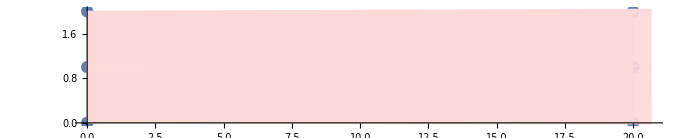

```mathematica
(*izris pomikov*)
scl=20;
voz1=voz+scl Ur;
Show[
ListPlot[voz],
Table[Graphics[{LightGray, EdgeForm[Thin], Polygon[Table[voz[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
Table[Graphics[{Opacity[0.9],LightRed, EdgeForm[Thin], Polygon[Table[voz1[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
PlotRange->All, AspectRatio->0.2
]
```

### Reševanje - napetosti

```mathematica
(*izračun napetosti*)
σel[koordinate_,Uele_,Em_,αm_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(* matrika elastičnih konstant *)
Dm=Em/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
(*relativni raztezek zaradi temperature*)
ϵ0=αm ΔT {1,1,0};
(*napetost v elementu*)
σstene=Dm.Be.Uele-Dm.ϵ0
]
(*napetost čez vse elemente*)
σ=Table[σel[voz[[ele[[i]]]],Flatten[Ur[[ele[[i]]]]], Evsi[[i]],αvsi[[i]]],{i,ste}];
σmin=Min/@(σᵀ);
σmax=Max/@(σᵀ);
```

#### Prikaz napetosti

```mathematica
(*tabela najmanjših in največjih napetosti*)
Grid[{{"","σxx","σyy","σxy"},
{"σmin",σmin[[1]],σmin[[2]],σmin[[3]]},
{"σmax",σmax[[1]],σmax[[2]],σmax[[3]]}}, Frame-> All]
```

| σxx | σyy | σxy
σmin | -91.2818 | -246.6 | -4.56409
σmax | 92.4306 | -0.114545 | 7.75508

```mathematica
(*Izris polja napetosti*)
komponenta=1(*1=σxx, 2=σyy, 3=σxy*);
{min,max}={σmin[[komponenta]],σmax[[komponenta]]};
Show[
ListPlot[voz1,PlotLegends->BarLegend[{"Rainbow",{min,max}}]],
Table[Graphics[{ColorData["Rainbow"][(σ[[j,komponenta]]-min)/(max-min)],EdgeForm[Thin],
Polygon[Table[voz1[[ele[[j,i]]]],{i,1,3}]]}],{j,1,ste}],
PlotRange->All,AspectRatio-> 0.2
]
```

-Graphics-

## Naloga 4

Za prikazani primer elementa izračunajte: 
- vozliščne pomike in 
- komponente napetostnega tenzorja
-Graphics-

```mathematica
(*Podatki*)
F=1000.(*N*);
g=9810. (*mm/s2*);
H=1000.(*mm*);
L=2000.(*mm*);
t=10.(*mm*);
Ej=210000.(*MPa*);
ν=0.3;
ρ=7800 10^-12(*ton/mm3*);

(* matrika elastičnih konstant *)
Dm=Ej/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});

(*teža stene - preliminarno*)
M=L*H*t*ρ*g;
```

### Definiramo vozlišča in končne elemente

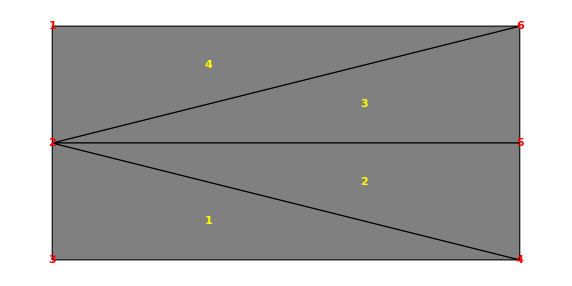

```mathematica
(*vozlišča in elementi*)
voz={
{0,H},{0,H/2},{0,0},{L,0},{L,H/2},{L,H}
};
ele={
{2,3,4},{2,4,5},{2,5,6},{1,2,6}
};

(*izris vseh elementov*)
stv=Length[voz];
ste=Length[ele];
P1=Table[Graphics[Text[Style[i,Medium,Bold, Red], voz[[i]]]],{i,1,stv}];
P2=Table[Graphics[Text[Style[i,Medium,Bold, Yellow], 1/3(voz[[ele[[i,1]]]]+voz[[ele[[i,2]]]]+voz[[ele[[i,3]]]])]],{i,1,ste}];
P3=Table[Graphics[{Gray, EdgeForm[Black],Polygon[voz[[ele[[j]]]]]}],{j,1,ste}];
Show[P3,P2, P1]
```

### Togostna matrika in vektor volumskih obremenitev posameznega elementa

```mathematica
Ke[koordinate_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*površina*)
Ω=Polygon[koordinate];
Ael=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika oblikovnih funkcij*)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(*togostna matrika elementa*)
Kele=t*Beᵀ.Dm.Be*Ael
]

Fv[koordinate_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*površina*)
Ω=Polygon[koordinate];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika oblikovnih funkcij*)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
(*vektor pospeška*)
ge={0,-g};
(*vektor temperaturnih obremenitev*)
Fvele=t*ρ*Integrate[Neᵀ.ge,{x,y}∈Ω]
]
```

### Globalna togostna matrika in vektor temperaturnih obremenitev

```mathematica
(*definiramo globalno togostno matriko in globalni vektor temperaturnih obremenitev*)
Kglob=Table[0,{i,1,2stv},{j,1,2stv}];
Fvglob=Table[0,{i,1,2stv}];
(*Prištejemo posamezne togostne matrike elementov*)
For[i=1, i≤ ste, i++,
{v1,v2,v3}=ele[[i]];
ps={2 v1-1,2v1,2v2-1,2v2,2v3-1,2v3};
Kglob[[ps,ps]]+=Ke[voz[[ele[[i]]]]];
Fvglob[[ps]]+=Fv[voz[[ele[[i]]]]]
]
MatrixForm[Kglob]
MatrixForm[Fvglob]
```

(1.90385×10^6 | -750000. | -1.61538×10^6 | 346154. | 0 | 0 | 0 | 0 | 0 | 0 | -288462. | 403846.
-750000. | 4.71635×10^6 | 403846. | -4.61538×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 346154. | -100962.
-1.61538×10^6 | 403846. | 3.80769×10^6 | 0. | -1.61538×10^6 | -403846. | 0. | 750000. | -576923. | 0. | 0. | -750000.
346154. | -4.61538×10^6 | 0. | 9.43269×10^6 | -346154. | -4.61538×10^6 | 750000. | 0. | 0. | -201923. | -750000. | 0.
0 | 0 | -1.61538×10^6 | -346154. | 1.90385×10^6 | 750000. | -288462. | -403846. | 0 | 0 | 0 | 0
0 | 0 | -403846. | -4.61538×10^6 | 750000. | 4.71635×10^6 | -346154. | -100962. | 0 | 0 | 0 | 0
0 | 0 | 0. | 750000. | -288462. | -346154. | 1.90385×10^6 | 0. | -1.61538×10^6 | -403846. | 0 | 0
0 | 0 | 750000. | 0. | -403846. | -100962. | 0. | 4.71635×10^6 | -346154. | -4.61538×10^6 | 0 | 0
0 | 0 | -576923. | 0. | 0 | 0 | -1.61538×10^6 | -346154. | 3.80769×10^6 | 0. | -1.61538×10^6 | 346154.
0 | 0 | 0. | -201923. | 0 | 0 | -403846. | -4.61538×10^6 | 0. | 9.43269×10^6 | 403846. | -4.61538×10^6
-288462. | 346154. | 0. | -750000. | 0 | 0 | 0 | 0 | -1.61538×10^6 | 403846. | 1.90385×10^6 | 0.
403846. | -100962. | -750000. | 0. | 0 | 0 | 0 | 0 | 346154. | -4.61538×10^6 | 0. | 4.71635×10^6)

(0.
-127.53
0.
-510.12
0.
-127.53
0.
-255.06
0.
-255.06
0.
-255.06)

### Vektor pomikov, vozliščnih sil in robni pogoji

```mathematica
(*pomiki in sile*)
Ui=Table[{Subscript[u, i],Subscript[v, i]},{i,1,stv}];
Fi=Table[{0,0},{i,1,stv}];
(*robni pogoji*)
rp={1,2,3};
Ui[[rp]]*=0;
Fi[[rp]]=Table[{Subscript[fx, i],Subscript[fy, i]},{i,rp}];
Print["Ui=",MatrixForm[Ui],"  Fi=",MatrixForm[Fi]]
```

Ui=(0 | 0
0 | 0
0 | 0
u_4 | v_4
u_5 | v_5
u_6 | v_6)  Fi=(fx_1 | fy_1
fx_2 | fy_2
fx_3 | fy_3
0 | 0
0 | 0
0 | 0)

### Reševanje - pomiki

```mathematica
rez=Solve[Kglob.Flatten[Ui]==Flatten[Fi]+Flatten[Fvglob]]
Ur=Ui/.Flatten[rez]
```

{{fx_1→-1530.36,fx_2→2.29832×10^-13,fx_3→1530.36,fy_1→702.257,fy_2→125.846,fy_3→702.257,u_4→-0.000701131,u_5→-5.21581×10^-20,u_6→0.000701131,v_4→-0.00328866,v_5→-0.00330533,v_6→-0.00328866}}

{{0,0},{0,0},{0,0},{-0.000701131,-0.00328866},{-5.21581×10^-20,-0.00330533},{0.000701131,-0.00328866}}

#### Prikaz pomikov

```mathematica
(*tabela pomikov*)
Grid[(Join[{{"voz", "ux [mm]","uy [mm]"}}, (Join[{Range[stv]}, Urᵀ]ᵀ)]),Frame->All]
```

voz | ux [mm] | uy [mm]
1 | 0 | 0
2 | 0 | 0
3 | 0 | 0
4 | -0.000701131 | -0.00328866
5 | -5.21581×10^-20 | -0.00330533
6 | 0.000701131 | -0.00328866

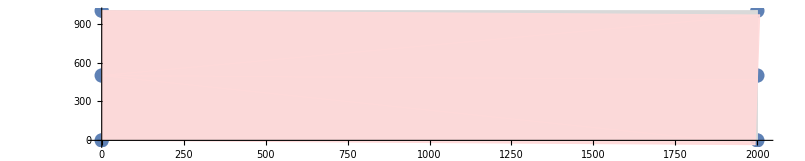

```mathematica
(*izris pomikov*)
scl=10000;
voz1=voz+scl Ur;
Show[
ListPlot[voz],
Table[Graphics[{LightGray, EdgeForm[Thin], Polygon[Table[voz[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
Table[Graphics[{Opacity[0.9],LightRed, EdgeForm[Thin], Polygon[Table[voz1[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
PlotRange->All, AspectRatio->0.2
]
```

### Reševanje - napetosti

```mathematica
(*izračun napetosti*)
σel[koordinate_,Uele_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(*napetost v elementu*)
σstene=Dm.Be.Uele
]
(*napetost čez vse elemente*)
σ=Table[σel[voz[[ele[[i]]]],Flatten[Ur[[ele[[i]]]]]],{i,ste}];
σmin=Min/@(σᵀ);
σmax=Max/@(σᵀ);
```

#### Prikaz napetosti

```mathematica
(*tabela najmanjših in največjih napetosti*)
Grid[{{"","σxx","σyy","σxy"},
{"σmin",σmin[[1]],σmin[[2]],σmin[[3]]},
{"σmax",σmax[[1]],σmax[[2]],σmax[[3]]}}, Frame-> All]
```

| σxx | σyy | σxy
σmin | -0.0808997 | -0.0242699 | -0.132811
σmax | 0.0808997 | 0.0242699 | -0.0202249

```mathematica
(*Izris polja napetosti*)
komponenta=1(*1=σxx, 2=σyy, 3=σxy*);
{min,max}={σmin[[komponenta]],σmax[[komponenta]]};
Show[
ListPlot[voz1,PlotLegends->BarLegend[{"Rainbow",{min,max}}]],
Table[Graphics[{ColorData["Rainbow"][(σ[[j,komponenta]]-min)/(max-min)],EdgeForm[Thin],
Polygon[Table[voz1[[ele[[j,i]]]],{i,1,3}]]}],{j,1,ste}],
PlotRange->All,AspectRatio-> 0.2
]
```

-Graphics-

## Naloga 5

Za prikazani primer krožne žage izračunajte: 
- vozliščne pomike in 
- komponente napetostnega tenzorja
-Graphics-

```mathematica
(*Podatki*)
R=300.(*mm*);
t=3.(*mm*);
Ej=210000.(*MPa*);
ν=0.3;
ρ=7800 10^-12(*ton/mm3*);
ω=1500*(2 π)/60.(*rad/s*);
(* matrika elastičnih konstant *)
Dm=Ej/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
```

### Definiramo vozlišča in končne elemente

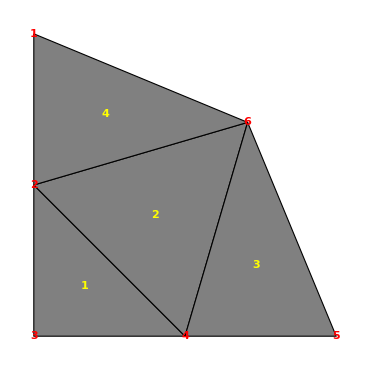

```mathematica
(*vozlišča in elementi*)
voz={
{0,R},{0,R/2},{0,0},{R/2,0},{R,0},{√2 R/2,√2 R/2}
};
ele={
{2,3,4},{2,4,6},{4,5,6},{1,2,6}
};

(*izris vseh elementov*)
stv=Length[voz];
ste=Length[ele];
P1=Table[Graphics[Text[Style[i,Medium,Bold, Red], voz[[i]]]],{i,1,stv}];
P2=Table[Graphics[Text[Style[i,Medium,Bold, Yellow], 1/3(voz[[ele[[i,1]]]]+voz[[ele[[i,2]]]]+voz[[ele[[i,3]]]])]],{i,1,ste}];
P3=Table[Graphics[{Gray, EdgeForm[Black],Polygon[voz[[ele[[j]]]]]}],{j,1,ste}];
Show[P3,P2, P1]
```

### Togostna matrika in vektor temperaturnih obremenitev posameznega elementa

```mathematica
Ke[koordinate_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*površina*)
Ω=Polygon[koordinate];
Ael=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika oblikovnih funkcij*)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(*togostna matrika elementa*)
Kele=t*Beᵀ.Dm.Be*Ael
]

Fv[koordinate_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*površina*)
Ω=Polygon[koordinate];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika oblikovnih funkcij*)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
(*vektor pospeška*)
a=ω^2{x,y};
(*vektor temperaturnih obremenitev*)
Fvele=t*ρ*Integrate[Neᵀ.a,{x,y}∈Ω]
]
```

### Globalna togostna matrika in vektor temperaturnih obremenitev

```mathematica
(*definiramo globalno togostno matriko in globalni vektor temperaturnih obremenitev*)
Kglob=Table[0,{i,1,2stv},{j,1,2stv}];
Fvglob=Table[0,{i,1,2stv}];
(*Prištejemo posamezne togostne matrike elementov*)
For[i=1, i≤ ste, i++,
{v1,v2,v3}=ele[[i]];
ps={2 v1-1,2v1,2v2-1,2v2,2v3-1,2v3};
Kglob[[ps,ps]]+=Ke[voz[[ele[[i]]]]];
Fvglob[[ps]]+=Fv[voz[[ele[[i]]]]]
]
MatrixForm[Kglob]
MatrixForm[Fvglob]
```

(213333. | -93198.1 | -111947. | -27955.8 | 0 | 0 | 0 | 0 | 0 | 0 | -101386. | 121154.
-93198.1 | 504234. | -10648.1 | -468749. | 0 | 0 | 0 | 0 | 0 | 0 | 103846. | -35485.1
-111947. | -10648.1 | 766487. | 59717.1 | -121154. | -121154. | -149715. | 246113. | 0 | 0 | -383671. | -174028.
-27955.8 | -468749. | 59717.1 | 1.03009×10^6 | -103846. | -346154. | 246113. | -149715. | 0 | 0 | -174028. | -65473.1
0 | 0 | -121154. | -103846. | 467308. | 225000. | -346154. | -121154. | 0 | 0 | 0 | 0
0 | 0 | -121154. | -346154. | 225000. | 467308. | -103846. | -121154. | 0 | 0 | 0 | 0
0 | 0 | -149715. | 246113. | -346154. | -103846. | 1.03009×10^6 | 59717.1 | -468749. | -27955.8 | -65473.1 | -174028.
0 | 0 | 246113. | -149715. | -121154. | -121154. | 59717.1 | 766487. | -10648.1 | -111947. | -174028. | -383671.
0 | 0 | 0 | 0 | 0 | 0 | -468749. | -10648.1 | 504234. | -93198.1 | -35485.1 | 103846.
0 | 0 | 0 | 0 | 0 | 0 | -27955.8 | -111947. | -93198.1 | 213333. | 121154. | -101386.
-101386. | 103846. | -383671. | -174028. | 0 | 0 | -65473.1 | -174028. | -35485.1 | 121154. | 586016. | 123057.
121154. | -35485.1 | -174028. | -65473.1 | 0 | 0 | -174028. | -383671. | 103846. | -101386. | 123057. | 586016.)

(162.386
736.506
601.982
1290.93
81.1929
81.1929
1290.93
601.982
736.506
162.386
1562.37
1562.37)

### Vektor pomikov, vozliščnih sil in robni pogoji

```mathematica
(*pomiki in sile*)
Ui=Table[{Subscript[u, i],Subscript[v, i]},{i,1,stv}];
Fi=Table[{0,0},{i,1,stv}];

(*robni pogoji*)
rpfix={3};
Ui[[rpfix]]*=0;
Fi[[rpfix]]=Table[{Subscript[fx, i],Subscript[fy, i]},{i,rpfix}];

rp1={1,2};
Ui[[rp1,{1}]]*=0;
Fi[[rp1,{1}]]=Table[Subscript[fx, i],{i,rp1}];

rp2={4,5};
Ui[[rp2,{2}]]*=0;
Fi[[rp2,{2}]]=Table[Subscript[fy, i],{i,rp2}];

Print["Ui=",MatrixForm[Ui],"  Fi=",MatrixForm[Fi]]
```

Ui=(0 | v_1
0 | v_2
0 | 0
u_4 | 0
u_5 | 0
u_6 | v_6)  Fi=(fx_1 | 0
fx_2 | 0
fx_3 | fy_3
0 | fy_4
0 | fy_5
0 | 0)

### Reševanje - pomiki

```mathematica
rez=Solve[Kglob.Flatten[Ui]==Flatten[Fi]+Flatten[Fvglob]]
Ur=Ui/.Flatten[rez];
```

{{fx_1→-544.085,fx_2→-2485.68,fx_3→-1405.6,fy_3→-1405.6,fy_4→-2485.68,fy_5→-544.085,u_4→0.00294312,u_5→0.00381298,u_6→0.00282988,v_1→0.00381298,v_2→0.00294312,v_6→0.00282988}}

#### Prikaz pomikov

```mathematica
(*tabela pomikov*)
Grid[(Join[{{"voz", "ux [mm]","uy [mm]"}}, (Join[{Range[stv]}, Urᵀ]ᵀ)]),Frame->All]
```

voz | ux [mm] | uy [mm]
1 | 0 | 0.00381298
2 | 0 | 0.00294312
3 | 0 | 0
4 | 0.00294312 | 0
5 | 0.00381298 | 0
6 | 0.00282988 | 0.00282988

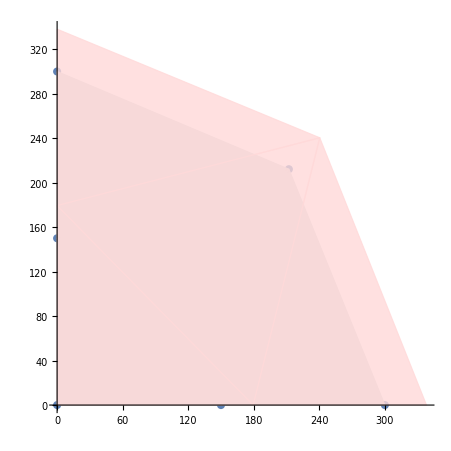

```mathematica
(*izris pomikov*)
scl=10000;
voz1=voz+scl Ur;
Show[
ListPlot[voz],
Table[Graphics[{LightGray, EdgeForm[Thin], Polygon[Table[voz[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
Table[Graphics[{Opacity[0.8],LightRed, EdgeForm[Thin], Polygon[Table[voz1[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
PlotRange->All, AspectRatio->1
]
```

### Reševanje - napetosti

```mathematica
(*izračun napetosti*)
σel[koordinate_,Uele_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(*napetost v elementu*)
σstene=Dm.Be.Uele
]
(*napetost čez vse elemente*)
σ=Table[σel[voz[[ele[[i]]]],Flatten[Ur[[ele[[i]]]]]],{i,ste}];
σmin=Min/@(σᵀ);
σmax=Max/@(σᵀ);
```

#### Prikaz napetosti

```mathematica
(*tabela najmanjših in največjih napetosti*)
Grid[{{"","σxx","σyy","σxy"},
{"σmin",σmin[[1]],σmin[[2]],σmin[[3]]},
{"σmax",σmax[[1]],σmax[[2]],σmax[[3]]}}, Frame-> All]
```

| σxx | σyy | σxy
σmin | 2.26181 | 2.26181 | -0.784721
σmax | 5.88624 | 5.88624 | 0.

```mathematica
(*Izris polja napetosti*)
komponenta=1(*1=σxx, 2=σyy, 3=σxy*);
{min,max}={σmin[[komponenta]],σmax[[komponenta]]};
Show[
ListPlot[voz1,PlotLegends->BarLegend[{"Rainbow",{min,max}}]],
Table[Graphics[{ColorData["Rainbow"][(σ[[j,komponenta]]-min)/(max-min)],EdgeForm[Thin],
Polygon[Table[voz1[[ele[[j,i]]]],{i,1,3}]]}],{j,1,ste}],
PlotRange->All,AspectRatio-> 1
]
```

-Graphics-

## Naloga 6

Za prikazani primer elementa izračunajte: 
- vozliščne pomike in 
- komponente napetostnega tenzorja
-Graphics-

```mathematica
(*Podatki*)
H=1000.(*mm*);
L=2000.(*mm*);
t=10.(*mm*);
Ej=210000.(*MPa*);
ν=0.3;
{p1,p2}={1.,2.}(*MPa*);
α=60°;

(* matrika elastičnih konstant *)
Dm=Ej/(1-ν^2)({{1, ν, 0}, {ν, 1, 0}, {0, 0, 1/2(1-ν)}});
```

### Definiramo vozlišča in končne elemente

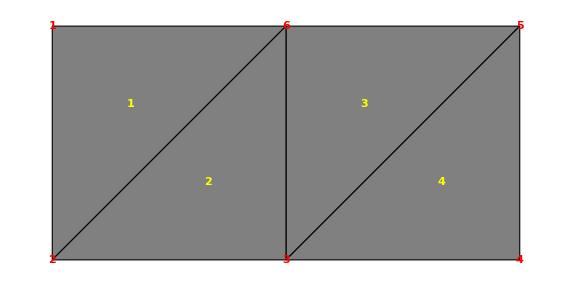

```mathematica
(*vozlišča in elementi*)
voz={
{0,H},{0,0},{L/2,0},{L,0},{L,H},{L/2,H}
};
ele={
{1,2,6},{2,3,6},{3,5,6},{3,4,5}
};

(*izris vseh elementov*)
stv=Length[voz];
ste=Length[ele];
P1=Table[Graphics[Text[Style[i,Medium,Bold, Red], voz[[i]]]],{i,1,stv}];
P2=Table[Graphics[Text[Style[i,Medium,Bold, Yellow], 1/3(voz[[ele[[i,1]]]]+voz[[ele[[i,2]]]]+voz[[ele[[i,3]]]])]],{i,1,ste}];
P3=Table[Graphics[{Gray, EdgeForm[Black],Polygon[voz[[ele[[j]]]]]}],{j,1,ste}];
Show[P3,P2, P1]
```

### Togostna matrika in vektor temperaturnih obremenitev posameznega elementa

```mathematica
Ke[koordinate_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*površina*)
Ω=Polygon[koordinate];
Ael=Area[Ω];
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika oblikovnih funkcij*)
Ne=({{ψi[x,y], 0, ψj[x,y], 0, ψk[x,y], 0}, {0, ψi[x,y], 0, ψj[x,y], 0, ψk[x,y]}});
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(*togostna matrika elementa*)
Kele=t*Beᵀ.Dm.Be*Ael
]
```

### Globalna togostna matrika in vektor temperaturnih obremenitev

```mathematica
(*definiramo globalno togostno matriko in globalni vektor temperaturnih obremenitev*)
Kglob=Table[0,{i,1,2stv},{j,1,2stv}];
Fvglob=Table[0,{i,1,2stv}];
(*Prištejemo posamezne togostne matrike elementov*)
For[i=1, i≤ ste, i++,
{v1,v2,v3}=ele[[i]];
ps={2 v1-1,2v1,2v2-1,2v2,2v3-1,2v3};
Kglob[[ps,ps]]+=Ke[voz[[ele[[i]]]]];
]
MatrixForm[Kglob]
```

(1.55769×10^6 | -750000. | -403846. | 346154. | 0 | 0 | 0 | 0 | 0 | 0 | -1.15385×10^6 | 403846.
-750000. | 1.55769×10^6 | 403846. | -1.15385×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 346154. | -403846.
-403846. | 403846. | 1.55769×10^6 | 0. | -1.15385×10^6 | 346154. | 0 | 0 | 0 | 0 | 0. | -750000.
346154. | -1.15385×10^6 | 0. | 1.55769×10^6 | 403846. | -403846. | 0 | 0 | 0 | 0 | -750000. | 0.
0 | 0 | -1.15385×10^6 | 403846. | 3.11538×10^6 | -750000. | -1.15385×10^6 | 346154. | 0. | -750000. | -807692. | 750000.
0 | 0 | 346154. | -403846. | -750000. | 3.11538×10^6 | 403846. | -403846. | -750000. | 0. | 750000. | -2.30769×10^6
0 | 0 | 0 | 0 | -1.15385×10^6 | 403846. | 1.55769×10^6 | -750000. | -403846. | 346154. | 0 | 0
0 | 0 | 0 | 0 | 346154. | -403846. | -750000. | 1.55769×10^6 | 403846. | -1.15385×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0. | -750000. | -403846. | 403846. | 1.55769×10^6 | 0. | -1.15385×10^6 | 346154.
0 | 0 | 0 | 0 | -750000. | 0. | 346154. | -1.15385×10^6 | 0. | 1.55769×10^6 | 403846. | -403846.
-1.15385×10^6 | 346154. | 0. | -750000. | -807692. | 750000. | 0 | 0 | -1.15385×10^6 | 403846. | 3.11538×10^6 | -750000.
403846. | -403846. | -750000. | 0. | 750000. | -2.30769×10^6 | 0 | 0 | 346154. | -403846. | -750000. | 3.11538×10^6)

### Vektor pomikov, vozliščnih sil, porazdeljenih sil in robni pogoji

```mathematica
(*pomiki in sile*)
Ui=Table[{Subscript[u, i],Subscript[v, i]},{i,1,stv}];
Fi=Table[{0,0},{i,1,stv}];
Fpglob=Table[{0,0},{i,1,stv}];
(*robni pogoji*)
rp={1,2,3};
Ui[[rp]]*=0;
Fi[[rp]]=Table[{Subscript[fx, i],Subscript[fy, i]},{i,rp}];
(*porazdeljena obremenitev*)
Fp1=p1*L/4*t;
Fp2=p1*H/2*t;

Fpglob[[1]]+=Fp1{Cos[α],-Sin[α]};
Fpglob[[6]]+=Fp1{Cos[α],-Sin[α]}+Fp1{Cos[α],-Sin[α]};
Fpglob[[5]]+=Fp1{Cos[α],-Sin[α]}+Fp2{0,-1};
Fpglob[[4]]+=Fp2{0,-1};

Print["Ui=",MatrixForm[Ui],"  Fi=",MatrixForm[Fi],"  Fp=",MatrixForm[Fp]]
```

Ui=(0 | 0
0 | 0
0 | 0
u_4 | v_4
u_5 | v_5
u_6 | v_6)  Fi=(fx_1 | fy_1
fx_2 | fy_2
fx_3 | fy_3
0 | 0
0 | 0
0 | 0)  Fp=(0
0
0
0
0
-2500.
0
-2500.
0
0
0
0)

### Reševanje - pomiki

```mathematica
rez=Solve[Kglob.Flatten[Ui]==Flatten[Fi]+Flatten[Fpglob]]
Ur=Ui/.Flatten[rez]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p1→0.,Kglob.{0,0,0,0,0,0,u_4,v_4,u_5,v_5,u_6,v_6}→0.,fx_1→0.,fx_2→0.,fx_3→0.,fy_1→0.,fy_2→0.,fy_3→0.}}

{{0,0},{0,0},{0,0},{u_4,v_4},{u_5,v_5},{u_6,v_6}}

#### Prikaz pomikov

```mathematica
(*tabela pomikov*)
Grid[(Join[{{"voz", "ux [mm]","uy [mm]"}}, (Join[{Range[stv]}, Urᵀ]ᵀ)]),Frame->All]
```

voz | ux [mm] | uy [mm]
1 | 0 | 0
2 | 0 | 0
3 | 0 | 0
4 | u_4 | v_4
5 | u_5 | v_5
6 | u_6 | v_6

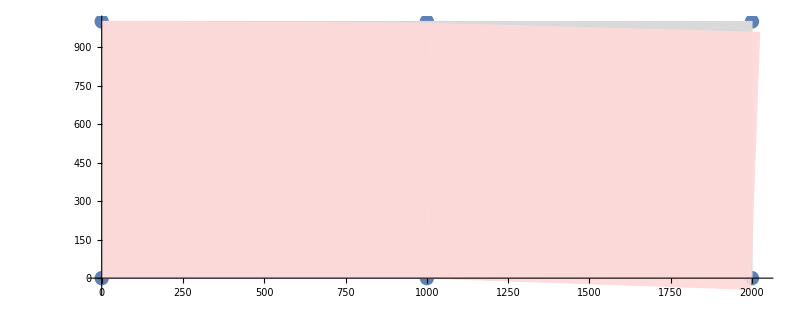

```mathematica
(*izris pomikov*)
scl=1000;
voz1=voz+scl Ur;
Show[
ListPlot[voz],
Table[Graphics[{LightGray, EdgeForm[Thin], Polygon[Table[voz[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
Table[Graphics[{Opacity[0.9],LightRed, EdgeForm[Thin], Polygon[Table[voz1[[ele[[j,i]]]], {i,1,3}]]}],{j,1,ste}],
PlotRange->All, AspectRatio->0.4
]
```

### Reševanje - napetosti

```mathematica
(*izračun napetosti*)
σel[koordinate_,Uele_]:=Module[{xi,yi,xj,yj,xk,yk},
{{xi,yi},{xj,yj},{xk,yk}}=koordinate;
(*oblikovne funkcije*)
ψ[x_,y_]=a1+a2 x+a3 y;
ψi[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==1,ψ[xj,yj]==0,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψj[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==1,ψ[xk,yk]==0},{a1,a2,a3}][[1]];
ψk[x_,y_]=ψ[x,y]/.Solve[{ψ[xi,yi]==0,ψ[xj,yj]==0,ψ[xk,yk]==1},{a1,a2,a3}][[1]];
(*matrika odvodov oblikovnih funkcij*)
Be=({{D[ψi[x,y], x], 0, D[ψj[x,y], x], 0, D[ψk[x,y], x], 0}, {0, D[ψi[x,y], y], 0, D[ψj[x,y], y], 0, D[ψk[x,y], y]}, {D[ψi[x,y], y], D[ψi[x,y], x], D[ψj[x,y], y], D[ψj[x,y], x], D[ψk[x,y], y], D[ψk[x,y], x]}});
(*napetost v elementu*)
σstene=Dm.Be.Uele
]
(*napetost čez vse elemente*)
σ=Table[σel[voz[[ele[[i]]]],Flatten[Ur[[ele[[i]]]]]],{i,ste}];
σmin=Min/@(σᵀ);
σmax=Max/@(σᵀ);
```

#### Prikaz napetosti

```mathematica
(*tabela najmanjših in največjih napetosti*)
Grid[{{"","σxx","σyy","σxy"},
{"σmin",σmin[[1]],σmin[[2]],σmin[[3]]},
{"σmax",σmax[[1]],σmax[[2]],σmax[[3]]}}, Frame-> All]
```

| σxx | σyy | σxy
σmin | -1.17226 | -1.73783 | -1.69377
σmax | 3.23409 | 0.970228 | 1.13193

```mathematica
(*Izris polja napetosti*)
komponenta=1(*1=σxx, 2=σyy, 3=σxy*);
{min,max}={σmin[[komponenta]],σmax[[komponenta]]};
Show[
ListPlot[voz1,PlotLegends->BarLegend[{"Rainbow",{min,max}}]],
Table[Graphics[{ColorData["Rainbow"][(σ[[j,komponenta]]-min)/(max-min)],EdgeForm[Thin],
Polygon[Table[voz1[[ele[[j,i]]]],{i,1,3}]]}],{j,1,ste}],
PlotRange->All,AspectRatio-> 0.2
]
```

-Graphics-

## Priprave za vajo 12

- obravnava primerov upogiba nosilca po MKE (eno polje in več polj)
- poznavanje (oz. razumevanje) enacbe koncnega elementa upogiba nosilca: 
- prostostne stopnje elementa (in pripadajoce sekundarne spremenljivke), 
- obravnava porazdeljene obremenitve, 
- oblikovne funkcije koncnega elementa.

## Naloga 1

Reševanje nosilca in palice.
-Graphics-

```mathematica
Ej = 210000;
Au=1000;
Iu=150 10^4;
F=2000.;
L=2000.;
α=30°;
q0=1;
```

### Analitika

```mathematica
(*Reševanje*)
w1[x_]=c0+c1 x+c2 x^2+c3 x^3+c4 x^4;
u1[x_]=d0+d1 x+d2 x^2;
N1[x_]:=Ej Au u1'[x];
M1[x_]:=-Ej Iu w1''[x];
T1[x_]:=M1'[x];

rez=NSolve[{
u1[0]==0,w1[0]==0, w1'[0]==0,

-N1[L] Sin[α]+T1[L]Cos[α]==0,
N1[L]Cos[α]+T1[L]Sin[α]-F==0,
M1[L]==0,
w1''''[x]==(q0 Sin[α])/(Ej Iu),
Ej Au u1''[x]==-q0 Cos[α]

}]
{w1[x_],u1[x_]}={w1[x],u1[x]}/.Flatten@rez;
```

{{c0→0.,c1→0.,c2→4.7619×10^-6,c3→-1.0582×10^-9,c4→6.61376×10^-14,d0→0.,d1→0.0000164957,d2→-2.06197×10^-9}}

```mathematica
(*Lokalni poves in raztezek*)
Plot[{w1[x]},{x,0,L}, AxesLabel->{"x [mm]","w1 [mm]"}]
Plot[{u1[x]},{x,0,L}, AxesLabel->{"x [mm]","u1 [mm]"}]
```

-Graphics-

-Graphics-

```mathematica
(*globalni pomiki*)
{ug2,vg2}= {u1[L] Sin[α]-w1[L]Cos[α],-u1[L]Cos[α]-w1[L]Sin[α]}
```

{-10.0683,-5.84153}

```mathematica
p1=ListLinePlot[{{0,0},{L Cos[α],-L Sin[α]}},PlotStyle->Black];
p2=ParametricPlot[RotationMatrix[-α].{x+10*u1[x],-10*w1[x]},{x,0,L},
PlotStyle->{Dashed,Red}];
Show[p1,p2,PlotRange->All]
```

-Graphics-

```mathematica
(*Napetosti*)
h=100;
σu[x_,y_]=M1[x]/Iu y;
σn[x_]=N1[x]/Au;
Plot[σu[x,h/2]+σn[x],{x,0,L},Filling->Axis,AxesOrigin->{0,0}]
```

-Graphics-

## Naloga 2

Obravnavaj ravninsko konstrukcijo.
-Graphics-

```mathematica
Ej = 210000;
Au=1000;
Iu=150 10^4;
F=2000.;
L=2000.;
α=30°;
```

### Analitika

```mathematica
L1=L2=L;

w1[x_]=c10+c11 x+c12 x^2+c13 x^3;
u1[x_]=d10+d11 x^2;
w2[x_]=c20+c21 x+c22 x^2+c23 x^3;
u2[x_]=d20+d21 x^2;

N1[x_]:=Ej Au u1'[x];
M1[x_]:=-Ej Iu w1''[x];
T1[x_]:=M1'[x];

N2[x_]:=Ej Au u2'[x];
M2[x_]:=-Ej Iu w2''[x];
T2[x_]:=M2'[x];

rez=NSolve[{
u1[0]==0,w1[0]==0,w1'[0]==0,

N2[L2]==F Sin[20°],
T2[L2]==F Cos[20°],
M2[L2]==0,

u1[L1]Cos[α]+w1[L1]Sin[α]==u2[0],
u1[L1]Sin[α]-w1[L1]Cos[α]==-w2[0],
w1'[L1]==w2'[0],
N2[0]-N1[L1]Cos[α]-T1[L1]Sin[α]==0,
-T2[0]+T1[L1]Cos[α]-N1[L1]Sin[α]==0,
M1[L1]==M2[0]
}]
```

{{c10→0.,c11→0.,c12→0.0000111333,c13→-8.61162×10^-10,c20→32.6027,c21→0.0341991,c22→5.9663×10^-6,c23→-9.94384×10^-10,d10→0.,d11→-1.11868×10^-9,d20→18.818,d21→8.14334×10^-10}}

```mathematica
(*globalni pomiki*)
{ug2,vg2}= {u2[0], -w2[0]}/.rez[[1]]
{ug3,vg3}= {u2[L2], -w2[L2]}/.rez[[1]]
```

{18.818,-32.6027}

{18.8213,-116.911}

- obravnava primerov upogiba nosilca po MKE (eno polje in več polj)
- poznavanje (oz. razumevanje) enacbe koncnega elementa upogiba nosilca: 
prostostne stopnje elementa (in pripadajoce sekundarne spremenljivke), 
obravnava porazdeljene obremenitve, 
oblikovne funkcije koncnega elementa.

## Naloga 3

Problem upogiba nosilca obravnavajte po MKE.

```mathematica
(*Podatki*)
L=2 10^3(*mm*);
M0=2 10^6(*N/mm*);
Ej=200000.(*MPa*);
Iu=171. 10^4(*mm^4*);
q0=5.(*N/mm*);
```

### Analitično

```mathematica
Clear[w]
NDSolve[{
w''''[x]==q0/(Ej Iu),
w[0]==0,w'[0]==0,
w[L]==0,-w''[L] Ej Iu==-M0
},w[x],x];
w[x_]=w[x]/.%[[1]];
pa=Plot[w[x],{x,0,L}];
```

### MKE

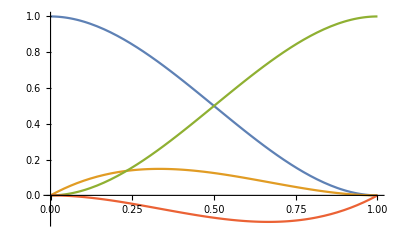

```mathematica
(*diskretizacija*)
ele=4;
h=L/ele;
n=2 ele+2;
(*Končni element*)
Ki[Ee_,Ie_,Le_]=(Ee Ie)/Le^3({{12, 6Le, -12, 6Le}, {6Le, 4 Le^2, -6Le, 2 Le^2}, {-12, -6Le, 12, -6Le}, {6Le, 2 Le^2, -6Le, 4 Le^2}});
ψ1[x_,Le_]=1-3(x/Le)^2+2(x/Le)^3;
ψ2[x_,Le_]=x-2 x^2/Le+x^3/Le^2;
ψ3[x_,Le_]=3 (x/Le)^2-2(x/Le)^3;
ψ4[x_,Le_]=-x^2/Le+x^3/Le^2;
Plot[{ψ1[x,1],ψ2[x,1],ψ3[x,1],ψ4[x,1]},{x,0,1}]
```

```mathematica
(*Definiramo matriko in vektorje*)
Kc=Table[0,{i,1,n},{j,1,n}];
Fi=Fq=Table[0,{i,1,n}];
wi=Table[Subscript[w, i],{i,1,n}];
(*globalna matrika*)
For[i=1,i≤ele,i++,
j=2i-1;
Kc[[{j,j+1,j+2,j+3},{j,j+1,j+2,j+3}]]+=Ki[Ej,Iu,h];
Fq1=Integrate[q0 ψ1[x,h],{x,0,h}];
Mq1=Integrate[q0 ψ2[x,h],{x,0,h}];
Fq2=Integrate[q0 ψ3[x,h],{x,0,h}];
Mq2=Integrate[q0 ψ4[x,h],{x,0,h}];
Fq[[j;;j+3]]+={Fq1,Mq1,Fq2,Mq2};
]
(*Robni pogoji*)
wi[[{1,2,-2}]]=0;
Fi[[1]]=Ra;
Fi[[2]]=Ma;
Fi[[-2]]=Rb;
Fi[[-1]]=M0;
NSolve[Kc.wi==Fi+Fq]
wi=wi/.%[[1]];
povesi=wi[[1;;-1;;2]]
Print[MatrixForm[Kc],MatrixForm[wi],"=",MatrixForm[Fi],MatrixForm[Fq]]
```

{{Ma→-1.5×10^6,Ra→-4750.,Rb→-5250.,w_3→0.296966,w_4→0.000761452,w_5→0.487329,w_6→-0.000121832,w_7→0.205592,w_8→-0.000822368,w_10→0.000487329}}

{0,0.296966,0.487329,0.205592,0}

(32832. | 8.208×10^6 | -32832. | 8.208×10^6 | 0 | 0 | 0 | 0 | 0 | 0
8.208×10^6 | 2.736×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0 | 0 | 0 | 0 | 0
-32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6 | 0 | 0 | 0 | 0
8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0 | 0 | 0
0 | 0 | -32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6 | 0 | 0
0 | 0 | 8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0
0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6
0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9
0 | 0 | 0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 32832. | -8.208×10^6
0 | 0 | 0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | -8.208×10^6 | 2.736×10^9)(0
0
0.296966
0.000761452
0.487329
-0.000121832
0.205592
-0.000822368
0
0.000487329)=(Ra
Ma
0
0
0
0
0
0
Rb
2000000)(1250.
104167.
2500.
1.16415×10^-10
2500.
1.16415×10^-10
2500.
1.16415×10^-10
1250.
-104167.)

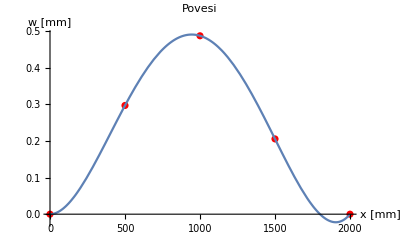

```mathematica
(*Izris upogiba*)
pMKE=ListPlot[Table[{(i-1)h,povesi[[i]]},{i,1,ele+1}],PlotLabel->"Povesi",AxesLabel->{"x [mm]","w [mm]"},PlotStyle->Red];
Show[pMKE,pa,PlotRange-> All]
```

## Naloga 4

```mathematica
(*Podatki*)
L=1 10^3(*mm*);
F0=2 10^3(*N*);
k=5000.(*N/mm*);
Ej=200000.(*MPa*);
{Iu1,Iu2}={342.,171.} 10^4(*mm^4*);
q0=5.(*N/mm*);
qx[x_]=q0-x/(2L) q0;
```

### Analitično

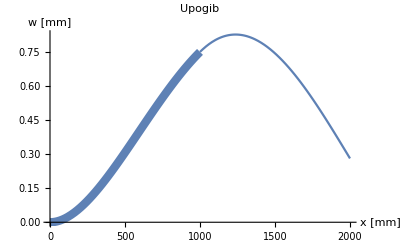

```mathematica
Clear[w1,w2]
NDSolve[{
w1''''[x]==qx[x]/(Ej Iu1),w2''''[x]==qx[x]/(Ej Iu2),
w1[0]==0,w1'[0]==0,-Ej Iu2 w2''[2L]==0,-Ej Iu2 w2'''[2L]==-k w2[2L],
w1[L]==w2[L],w1'[L]==w2'[L],-Ej Iu1 w1''[L]==-Ej Iu2 w2''[L],-Ej Iu1 w1'''[L]==-Ej Iu2 w2'''[L]+F0
},{w1[x],w2[x]},x];
{w1[x_],w2[x_]}={w1[x],w2[x]}/.%[[1]];
p1a=Plot[w1[x],{x,0,L},PlotLabel->"Upogib",AxesLabel->{"x [mm]","w [mm]"},PlotStyle->{Thickness[0.015]}];
p2a=Plot[w2[x],{x,L,2L}];
Show[p1a,p2a,PlotRange->All]
```

### MKE

```mathematica
(*diskretizacija*)
ele=2;
h=L/ele;
n=2 ele+2ele+2;
(*Končni element*)
Ki[Ee_,Ie_,Le_]=(Ee Ie)/Le^3({{12, 6Le, -12, 6Le}, {6Le, 4 Le^2, -6Le, 2 Le^2}, {-12, -6Le, 12, -6Le}, {6Le, 2 Le^2, -6Le, 4 Le^2}});
ψ1[x_,Le_]=1-3(x/Le)^2+2(x/Le)^3;
ψ2[x_,Le_]=x-2 x^2/Le+x^3/Le^2;
ψ3[x_,Le_]=3 (x/Le)^2-2(x/Le)^3;
ψ4[x_,Le_]=-x^2/Le+x^3/Le^2;
(*Matrika in vektorji*)
Kc=Table[0,{i,1,n},{j,1,n}];
Fi=Fq=Table[0,{i,1,n}];
wi=Table[Subscript[w, i],{i,1,n}];
(*Kc1*)
For[i=1,i≤ele,i++,
j=2i-1;
Kc[[{j,j+1,j+2,j+3},{j,j+1,j+2,j+3}]]+=Ki[Ej,Iu1,h];
x0=(i-1)h;
Fq1=Integrate[qx[x0+x] ψ1[x,h],{x,0,h}];
Mq1=Integrate[qx[x0+x] ψ2[x,h],{x,0,h}];
Fq2=Integrate[qx[x0+x] ψ3[x,h],{x,0,h}];
Mq2=Integrate[qx[x0+x] ψ4[x,h],{x,0,h}];
Fq[[j;;j+3]]+={Fq1,Mq1,Fq2,Mq2};
]
(*Kc2*)
For[i=ele+1,i≤ele+ele,i++,
j=2i-1;
Kc[[{j,j+1,j+2,j+3},{j,j+1,j+2,j+3}]]+=Ki[Ej,Iu2,h];
x0=(i-1)h;
Fq1=Integrate[qx[x0+x] ψ1[x,h],{x,0,h}];
Mq1=Integrate[qx[x0+x] ψ2[x,h],{x,0,h}];
Fq2=Integrate[qx[x0+x] ψ3[x,h],{x,0,h}];
Mq2=Integrate[qx[x0+x] ψ4[x,h],{x,0,h}];
Fq[[j;;j+3]]+={Fq1,Mq1,Fq2,Mq2};
]
(*RP*)
wi[[{1,2}]]={0,0};
Fi[[{1,2,-2,-1}]]={Ra,Ma,-k wi[[-2]],0};
(*PKP*)
Fi[[2ele+1]]=F0;
(*Solve*)
NSolve[Kc.wi==Fq+Fi];
wi=wi/.%[[1]];
povesi=wi[[1;;-1;;2]]
Print[MatrixForm[Kc],MatrixForm[wi],"=",MatrixForm[Fi],"+",MatrixForm[Fq]]
```

{0,0.307796,0.751685,0.745403,0.281603}

(65664. | 1.6416×10^7 | -65664. | 1.6416×10^7 | 0 | 0 | 0 | 0 | 0 | 0
1.6416×10^7 | 5.472×10^9 | -1.6416×10^7 | 2.736×10^9 | 0 | 0 | 0 | 0 | 0 | 0
-65664. | -1.6416×10^7 | 131328. | 0. | -65664. | 1.6416×10^7 | 0 | 0 | 0 | 0
1.6416×10^7 | 2.736×10^9 | 0. | 1.0944×10^10 | -1.6416×10^7 | 2.736×10^9 | 0 | 0 | 0 | 0
0 | 0 | -65664. | -1.6416×10^7 | 98496. | -8.208×10^6 | -32832. | 8.208×10^6 | 0 | 0
0 | 0 | 1.6416×10^7 | 2.736×10^9 | -8.208×10^6 | 8.208×10^9 | -8.208×10^6 | 1.368×10^9 | 0 | 0
0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 65664. | 0. | -32832. | 8.208×10^6
0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | 0. | 5.472×10^9 | -8.208×10^6 | 1.368×10^9
0 | 0 | 0 | 0 | 0 | 0 | -32832. | -8.208×10^6 | 32832. | -8.208×10^6
0 | 0 | 0 | 0 | 0 | 0 | 8.208×10^6 | 1.368×10^9 | -8.208×10^6 | 2.736×10^9)(0
0
0.307796
0.000960977
0.751685
0.000658589
0.745403
-0.000599744
0.281603
-0.00109533)=(Ra
Ma
0
0
2000
0
0
0
-5000. w_9
0)+(1156.25
93750.
1875.
-20833.3
1250.
-20833.3
625.
-20833.3
93.75
-10416.7)

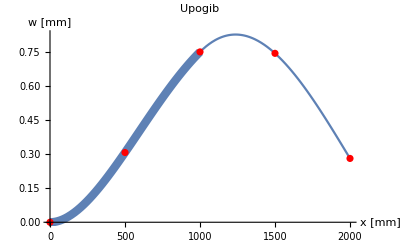

```mathematica
(*izris*)
p=ListPlot[Table[{(i-1)h,povesi[[i]]},{i,1,ele+ele+1}],PlotStyle->Red];
Show[p1a,p2a,p,PlotRange-> All]
```